## Multi-locos Deterministic model

### Dependencies

```mathematica
(*Accept a number and number of loci convert it to the binary format with the assigned digits (here loci)*)
Convert[y0_,x0_]:= Module[{u=y0,b=0,j=0,w=0,r=0,a=0,s="",x=x0},
b:=u;
j:=b;
w:=0;
r:=0;
If[u==1,
r=1,
If[u==0,
r=0,
While[b>=1,j=Mod[b,2];r=j*10^w+r;w++;b=Quotient[b,2]]
]
];
s=ToString[r];
If[Length[IntegerDigits[r]]≤ x ,
a=Length[IntegerDigits[r]];
While[a< x,s=StringJoin[{"0"},{s}];a++];
,a=1];
s
]
```

```mathematica
(*Accept a string in binary format and convert it to ten base format*)
Binary[s0_]:=Module[{v=s0,k=0,s=0, b="",z1=1},
If[v>1,
k:=Length[IntegerDigits[v]];
b= ToString[v];
s:=0;
While[k≥1, s=ToExpression[StringTake[b,{z1,z1}]]2^(k-1)+s; k--; z1++];
s
,
If[v==1,s=1,s=0]
s
]
]
```

### Equations

```mathematica
locus=2;
dnasize=1;
Clear[selection,foodvalue,basegrowth,uptake,degredation,mutation,death,cost,fratricide];
selection=selection;
foodvalue=foodvalue;
capacity= 100000000;
basegrowth=basegrowth;
uptake=uptake;
degradation=degredation;
mut=mutation;
death=death;
cost=cost;
fratricide=fratricide;
portion=portion;
Fitness=Table[0,{i,1,2^locus}];
Checkf[x0_, y0_,m0_]:=Module[{s1=x0,s2=y0,n=m0},s1=StringTake[s1,{n,n+StringLength[s2]-1}];StringMatchQ[s1,s2]]



Do[Fitness[[2^locus-i+1]]=((StringCount[Convert[i-1,locus],"1"]*selection))+death;,{i,1,(2^locus)}]

intitialff=Array[Subscript[ff,#][0]&,3*2^locus+2^dnasize*(locus-dnasize+1)];
initialf=Table[0,{i,3*2^locus+2^dnasize*(locus-dnasize+1)}];
initialf[[1]]=30000000;
initialf[[1+2^locus]]=30000000;
initialf[[1+2*2^locus]]=0;
ffunction=Array[Subscript[ff,#][t]&,{3*2^locus+2^dnasize*(locus-dnasize+1)}];
recombinationm=Table["",{2^locus},{2^dnasize*(locus-dnasize+1)}];
sizefrag=2^dnasize*(locus-dnasize+1);
derivationl=Array[Subscript[ff',#][t]&,{3*2^locus+2^dnasize*(locus-dnasize+1)}];
Do[derivationl[[i]]=0,{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}]
derivationr=D[ffunction,t];


sum=0;Do[sum=sum+ffunction[[i]];,{i,1,3*2^locus}];sum;
sumc=0;Do[sumc=sumc+ffunction[[i]];,{i,1,2*2^locus}];sumc;
sumf=0;Do[sumf=sumf+ffunction[[i]];,{i,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}];sumf;



Do[
s1=Convert[m-1,locus];
holder=StringTake[s1,{Quotient[(n-1),(2^dnasize)]+1,Quotient[(n-1),(2^dnasize)]+dnasize}];
s2=Convert[Mod[(n-1),(2^dnasize)],dnasize];
p=StringReplacePart[s1,s2,{Quotient[(n-1),(2^dnasize)]+1,Quotient[(n-1),(2^dnasize)]+dnasize}];
recombinationm[[m,n]]=p;
,{m,1,2^locus},{n,1,sizefrag}]
MatrixForm[recombinationm]


Do[derivationl[[n]]=derivationl[[n]]+ffunction[[n]]*(basegrowth+foodvalue*uptake*(sumf)-cost)*(1-(sum)/capacity)-ffunction[[n]]*Fitness[[n]];,{n,1,2^locus}]
Do[derivationl[[m]]=derivationl[[m]]-uptake*portion*ffunction[[m]]*ffunction[[3*2^locus+n]]; ,{m,1,2^locus},{n,1,sizefrag}]
Do[derivationl[[Binary[ToExpression[recombinationm[[m,n]]]]+1]]=derivationl[[Binary[ToExpression[recombinationm[[m,n]]]]+1]]+uptake*portion*ffunction[[m]]*ffunction[[3*2^locus+n]]; ,{m,1,2^locus},{n,1,sizefrag}]




Do[
Do[If[HammingDistance[Convert[n-1,locus],Convert[m-1,locus]]==1,
derivationl[[n]]=derivationl[[n]]+mut*ffunction[[m]]
]
,{m,1,2^locus}];
derivationl[[n]]=derivationl[[n]]- mut*locus*ffunction[[n]];
,{n,1,2^locus}]




Do[derivationl[[n]]=derivationl[[n]]+ffunction[[n]]*(basegrowth+foodvalue*uptake*(sumf)-cost)*(1-(sum)/capacity)-ffunction[[n]]*Fitness[[n-2^locus]];,{n,2^locus+1,2*2^locus}]
Do[
Do[If[HammingDistance[Convert[n-1,locus],Convert[m-1,locus]]==1,
derivationl[[n]]=derivationl[[n]]+mut*ffunction[[m]]
]
,{m,2^locus+1,2*2^locus}];
derivationl[[n]]=derivationl[[n]]- mut*locus*ffunction[[n]];
,{n,2^locus+1,2*2^locus}]
derivationl;


Do[derivationl[[n]]=derivationl[[n]]+ffunction[[n]]*(basegrowth)*(1-(sum)/capacity)-ffunction[[n]]*Fitness[[n-2*2^locus]]-sumc*fratricide*ffunction[[n]];,{n,2*2^locus+1,3*2^locus}]

Do[
Do[If[HammingDistance[Convert[n-1,locus],Convert[m-1,locus]]==1,
derivationl[[n]]=derivationl[[n]]+mut*ffunction[[m]];
]
,{m,2*2^locus+1,3*2^locus}];
derivationl[[n]]=derivationl[[n]]- mut*locus*ffunction[[n]];
,{n,2*2^locus+1,3*2^locus}]

Do[
(*derivationl[[n]]=derivationl[[n]]-ffunction[[n]]*uptake*sumc-degradation*ffunction[[n]];*)
derivationl[[n]]=derivationl[[n]]-degradation*ffunction[[n]];
,{n,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]

Checkf[x0_, y0_,m0_]:=Module[{s1=x0,s2=y0,n=m0},s1=StringTake[s1,{n,n+StringLength[s2]-1}];StringMatchQ[s1,s2]]
Do[
s2=Convert[Mod[(n-1),(2^dnasize)],dnasize];
If[Checkf[Convert[m-1,locus],s2,Quotient[n-1,(2^dnasize)]+1],
derivationl[[n+3*2^locus]]=derivationl[[n+3*2^locus]]+(ffunction[[m]]*Fitness[[m]])/(locus-dnasize+1);
derivationl[[n+3*2^locus]]=derivationl[[n+3*2^locus]]+(ffunction[[m+2^locus]]*Fitness[[m]])/(locus-dnasize+1);
derivationl[[n+3*2^locus]]=derivationl[[n+3*2^locus]]+(ffunction[[m+2*2^locus]]*Fitness[[m]]+sumc*fratricide*ffunction[[m+2*2^locus]])/(locus-dnasize+1);
];
,{m,1,2^locus},{n,1,2^dnasize*(locus-dnasize+1)}]

sys11=Join[  Table[ 0==derivationl[[i]],{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}]];


sys1=Join[  Table[ derivationr[[i]]==derivationl[[i]],{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}],Table[ intitialff[[i]]== initialf[[i]],{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}]];
sys1;

5000000
500000
50000
po=100000;
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.0000000000001, death->0.001,cost ->0,fratricide ->0,portion-> 1},ffunction,{t,0,po}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001, degredation->0,mutation->0.0000000000001, death->0.005,cost ->0,fratricide ->0,portion->1},ffunction,{t,0,po}];(*browne*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.0000000000001, death->0.06,cost ->0,fratricide ->0,portion -> 1},ffunction,{t,0,po}];(*blue,Method->"StiffnessSwitching"*dotted*)

rec=0;Do[rec=rec+ffunction[[m]],{m,1,2^locus}] ;
nut=0;Do[nut=nut+ffunction[[m]],{m,2^locus+1,2*2^locus}] ;
non=0;Do[non=non+ffunction[[m]],{m,2*2^locus+1,3*2^locus}] ;
```

(00 | 10 | 00 | 01
01 | 11 | 00 | 01
00 | 10 | 10 | 11
01 | 11 | 10 | 11)

5000000

500000

50000

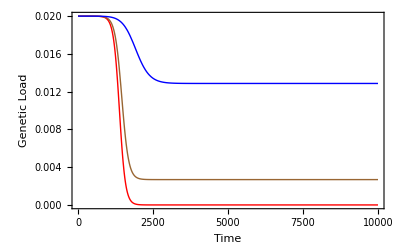

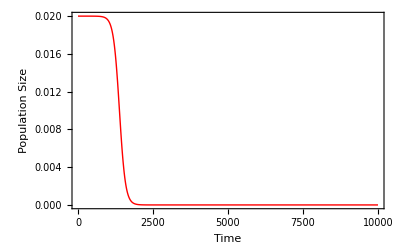

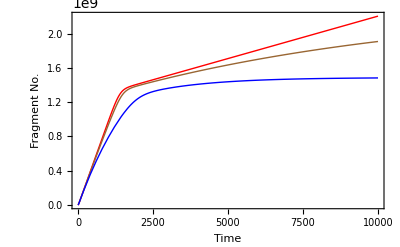

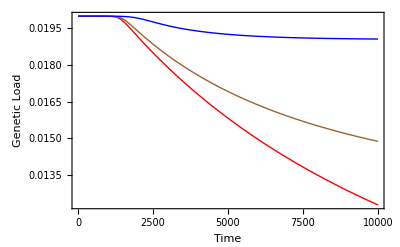

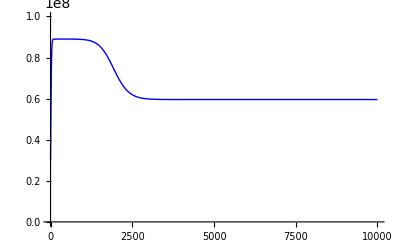

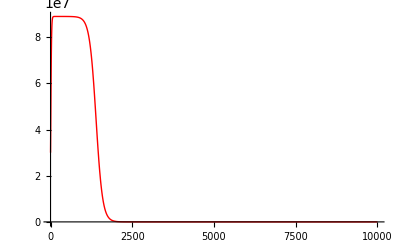

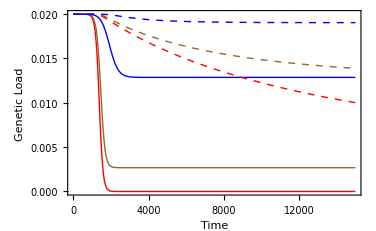

```mathematica
sol2=NDSolve[sys1/. {selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.000000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.000000000005,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

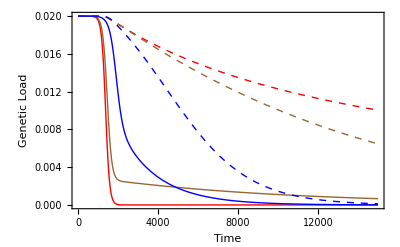

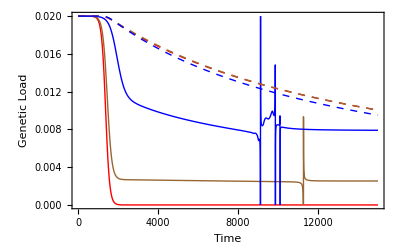

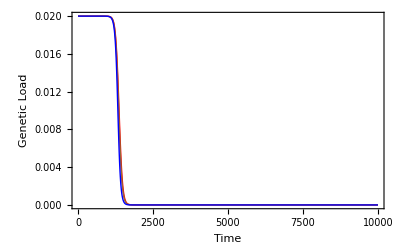

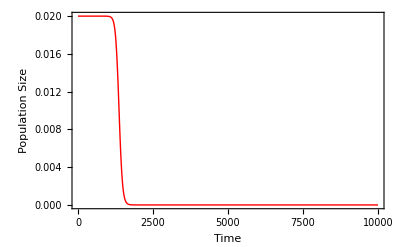

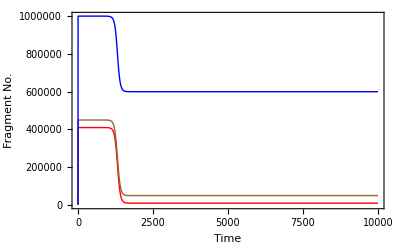

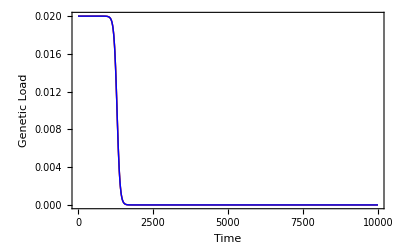

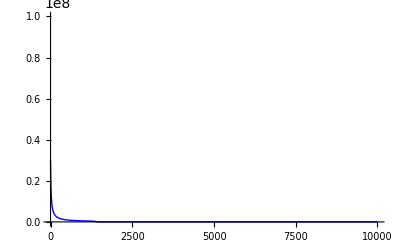

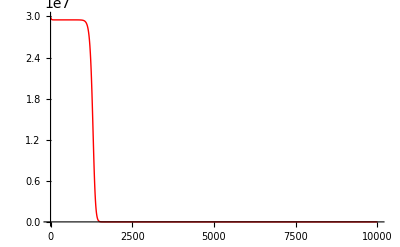

{{1,0.0726518},{0.001,0.0726391},{0.0001, 0.0726368},{0.000001,0.072385},{0.00000001,0.050893},{0.0000000001,4.17692×10^-7},{0.000000000001,0.00032285},{0.00000000000001,0.470149},{0.0000000000000001,0.4997},{0.000000000000000001,0.499997},{0.00000000000000000001,0.5}}

{0.001,0.0726391}

{0.0001, 0.0726368}

{0.000001,0.072385}

{0.00000001,0.050893}

{0.0000000001,4.17692×10^-7}

{0.000000000001,0.00032285}

{0.00000000000001,0.470149}

{0.0000000000000001,0.4997}

{0.000000000000000001,0.499997}

{0.00000000000000000001,0.5}

```mathematica
Show[
Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Red,Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol3],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Brown,Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol4],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Blue,Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]



Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Population Size"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Red,Frame -> True]

Show[
Plot[Evaluate[sumf  /.sol2],{t,0,10000},FrameLabel->{"Time","Fragment No."},PlotRange ->All,LabelStyle->16 ,PlotStyle ->Red],
Plot[Evaluate[sumf  /.sol3],{t,0,10000},FrameLabel->{"Time","Fragment No."},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Brown],
Plot[Evaluate[sumf  /.sol4],{t,0,10000},FrameLabel->{"Time","Fragment No."},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Blue]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]

Show[
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle ->Red],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])   /.sol3],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Brown],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol4],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Blue]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]

Plot[Evaluate[ffunction[[1]]  /.sol4],{t,0,10000},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> Blue]
Plot[Evaluate[ffunction[[1]]  /.sol2],{t,0,10000},FrameLabel->{"Time","Population Size"},PlotRange ->All, LabelStyle->16 ,PlotStyle -> Red]

g=po;
Show[
Show[
Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Red,Thick},Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol3],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Brown,Thick},Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol4],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Blue,Thick},Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
,
Show[
Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Red,Dotted},Frame -> True],

Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol3],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Brown,Dotted},Frame -> True],

Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol4],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle ->{Blue,Dotted},Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
,
Show[
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle ->{Red,Thick,Dashed}],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])   /.sol3],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> {Brown,Thick,Dashed}],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol4],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> { Blue,Thick,Dashed}]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
]



Show[
Show[
Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->20 ,PlotStyle -> {Blue,Thick},Frame -> True],

Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->20}
]
,
Show[
Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->20 ,PlotStyle -> {Blue,Dotted},Frame -> True],

Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->20}
]
,
Show[
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->20,PlotStyle ->{Blue,Thick,Dashed}],
Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->20}
]
]


Show[
Show[
Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol4],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->20 ,PlotStyle -> {Red,Thick},Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol3],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->20 ,PlotStyle -> {Green,Thick},Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->20 ,PlotStyle -> {Blue,Thick},Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->20}
]

,
Show[
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol4],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle ->{Red,Thick,Dashed}],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])   /.sol3],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> {Green,Thick,Dashed}],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> { Blue,Thick,Dashed}]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->20}
]
]
```

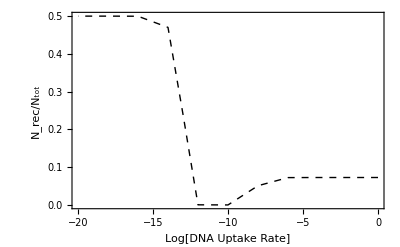

```mathematica
ListPlot[{{0,0.0726518},{-3,0.0726391},{-4, 0.0726368},{-6,0.072385},{-8,0.050893},{-10,4.17692×10^-7},{-12,0.00032285},{-13,0.23992285210799838},{-14,0.470149},{-16,0.4997},{-18,0.499997},{-20,0.5}},Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16},Joined -> True,PlotStyle ->{ Black,Thick,Dashed},FrameLabel -> {"Log[DNA Uptake Rate]" ,Subscript[N,"rec"]/ Subscript[N,"tot"]}]
```

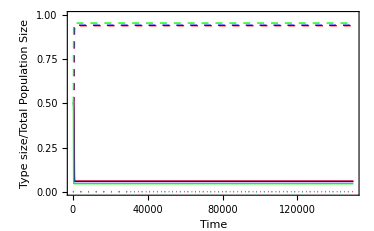
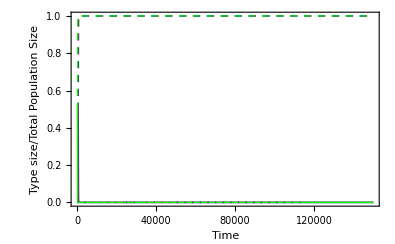
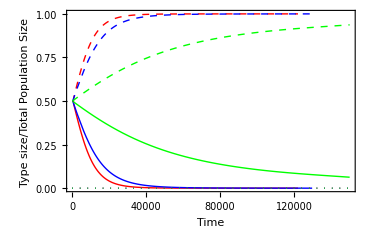

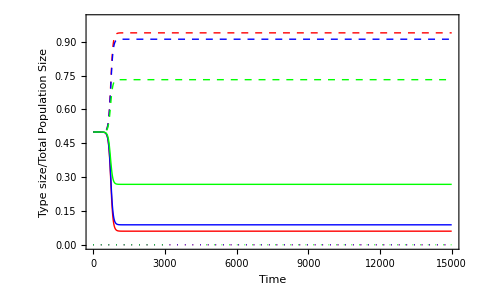
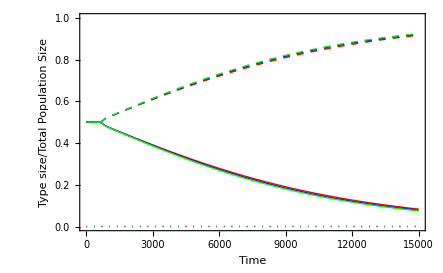

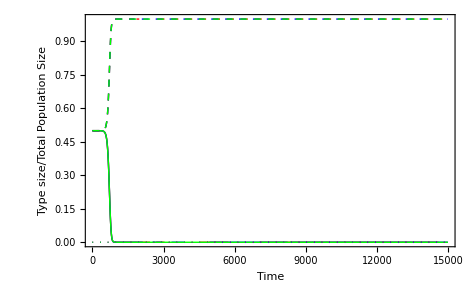

```mathematica
{{0,0.0726518},{-3,0.0726391},{-4, 0.0726368},{-6,0.072385},{-8,0.050893},{-10,4.17692×10^-7},{-12,0.00032285},{-13,0.23992285210799838},{-14,0.470149},{-16,0.4997},{-18,0.499997},{-20,0.5}}
```

{{0,0.0726518},{-3,0.0726391},{-4,0.0726368},{-6,0.072385},{-8,0.050893},{-10,4.17692×10^-7},{-12,0.00032285},{-13,0.239923},{-14,0.470149},{-16,0.4997},{-18,0.499997},{-20,0.5}}

### Plotting

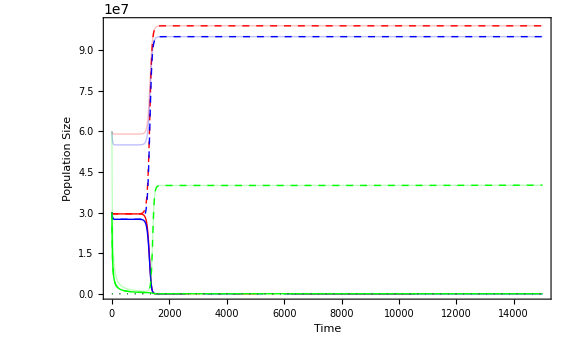

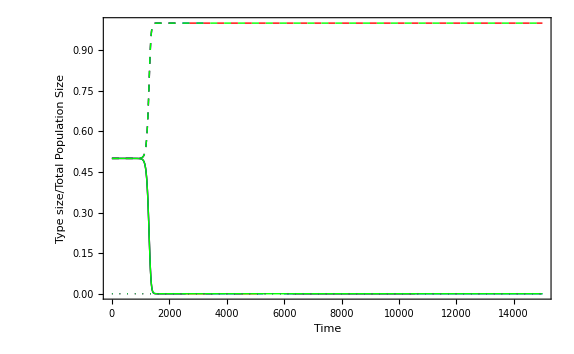

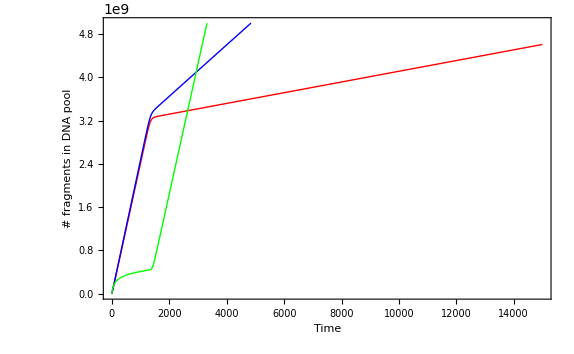

(selection ff_13[t]+selection ff_15[t])/(ff_13[t]+ff_14[t]+ff_15[t]+ff_16[t])

{0.04,0.02,0.02,0}

15000

{0.04,0.02,0.02,0}

15000

{0.04,0.02,0.02,0}

15000

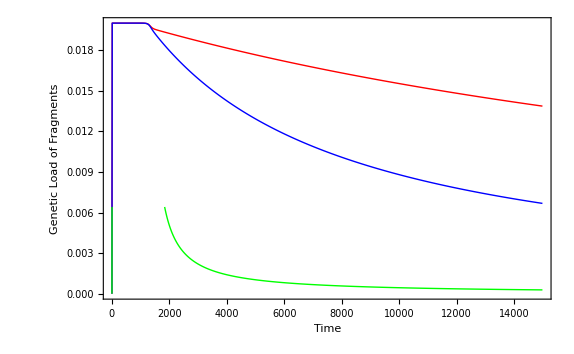

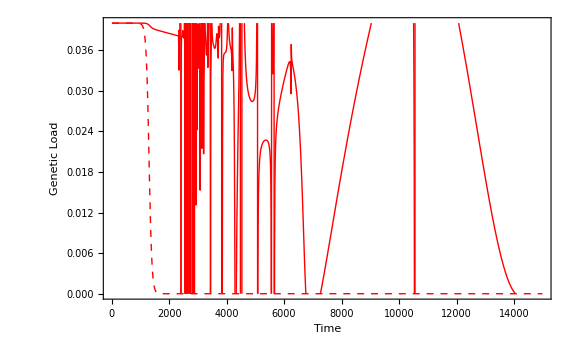

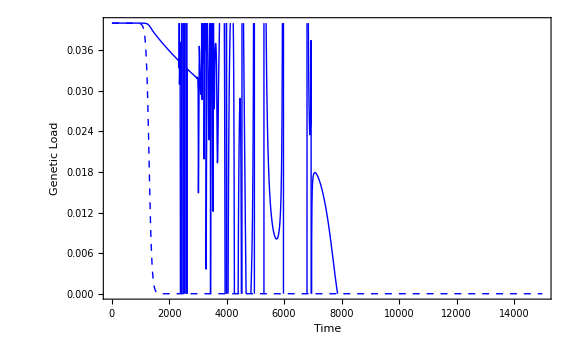

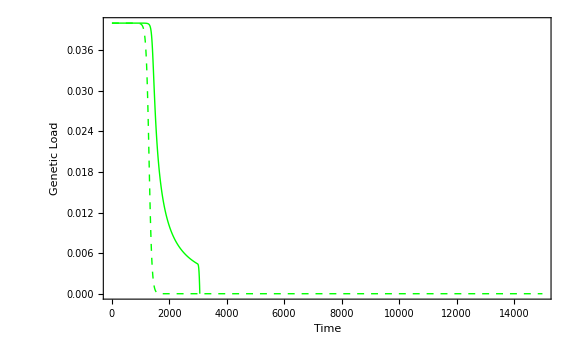

```mathematica
g=15000;
Show[
Plot[Evaluate[rec  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle -> Red]
,
Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> Blue]
,
Plot[Evaluate[rec/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle -> Green]
,
Plot[Evaluate[nut  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle -> {Red,Dashed}]
,
Plot[Evaluate[nut  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Blue,Dashed}]
,
Plot[Evaluate[nut/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Green,Dashed}]
,
Plot[Evaluate[non /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle -> {Red,Dotted}]
,
Plot[Evaluate[non  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Blue,Dotted}]
,
Plot[Evaluate[non/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Green,Dotted}]
,
Plot[Evaluate[sum  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle -> {Red,Opacity[0.25],Thick}]
,
Plot[Evaluate[sum  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Blue,Opacity[0.25],Thick}]
,
Plot[Evaluate[sum/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Green,Opacity[0.25],Thick}]
,
 Frame -> True,AxesOrigin->{0,0}
]



Show[
Plot[Evaluate[rec/sum  /.sol2],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1}, LabelStyle->16 ,PlotStyle -> Red]
,
Plot[Evaluate[rec/sum  /.sol3],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1},LabelStyle->16 ,PlotStyle -> Blue]
,
Plot[Evaluate[rec/sum /.sol4],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1},LabelStyle->16,PlotStyle -> Green]
,
Plot[Evaluate[nut/sum  /.sol2],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1}, LabelStyle->16 ,PlotStyle -> {Red,Dashed}]
,
Plot[Evaluate[nut/sum  /.sol3],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1},LabelStyle->16 ,PlotStyle -> {Blue,Dashed}]
,
Plot[Evaluate[nut/sum /.sol4],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1},LabelStyle->16,PlotStyle ->{Green,Dashed}]
,

Plot[Evaluate[non/sum  /.sol2],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1}, LabelStyle->16 ,PlotStyle -> {Red,Dotted}]
,
Plot[Evaluate[non/sum  /.sol3],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1},LabelStyle->16 ,PlotStyle -> {Blue,Dotted}]
,
Plot[Evaluate[non/sum /.sol4],{t,0,g},FrameLabel->{"Time","Type size/Total Population Size"},PlotRange ->{0,1},LabelStyle->16,PlotStyle ->{Green,Dotted}]
,

 Frame -> True,AxesOrigin->{0,0}
]

(*RangeFragments=1000000;*)
RangeFragments=5000000000;
Show[
Plot[Evaluate[sumf  /.sol2],{t,0,g},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,RangeFragments}, LabelStyle->16 ,PlotStyle -> Red]
,
Plot[Evaluate[sumf /.sol3],{t,0,g},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,RangeFragments},LabelStyle->16 ,PlotStyle -> Blue]
,
Plot[Evaluate[sumf/.sol4],{t,0,g},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,RangeFragments},LabelStyle->16,PlotStyle -> Green]
, Frame -> True,AxesOrigin->{0,0}
]






Mutloadfrag=0;
Do[
Mutloadfrag=Mutloadfrag+StringCount[Convert[Mod[m-1,2^dnasize],dnasize],"0"]*selection*ffunction[[3*2^locus+m]];
,{m,1,2^dnasize*(locus-dnasize+1)}]
Mutloadfrag=Mutloadfrag/sumf



Fitness1=Evaluate[Fitness] /. {selection ->0.02,death->0}

up=g;
time=10;death=0;selection=0.02;loadr=0;loadn=0;loadu=0;mutloadr1={};mutloadn1={};mutloadu1={};mutloadf1={};
holder=0;
bf="";
Print[up];


mutloadf1=Append[mutloadf1,{0,0}];

While[time < up,          
loadr=0;
Do[
holder=Evaluate[(ffunction[[m]]*(Fitness1[[m]]))/rec /.sol2]  /.{t-> time};
loadr=loadr+holder[[1]];
,{m,1,2^locus}];
mutloadr1=Append[mutloadr1,{time,loadr}];


loadn=0;
Do[
holder=Evaluate[ffunction[[m]]*(Fitness1[[m-2^locus]])/nut /.sol2]  /.{t-> time};
loadn=loadn+holder[[1]];
,{m,2^locus+1,2*2^locus}];
mutloadn1=Append[mutloadn1,{time,loadn}];



loadu=0;
Do[
holder=Evaluate[ffunction[[m]]*(Fitness1[[m-2*2^locus]])/non /.sol2]  /.{t-> time};
loadu=loadu+holder[[1]];
,{m,2*2^locus+1,3*2^locus}];
mutloadu1=Append[mutloadu1,{time,loadu}];


holder=Evaluate[Mutloadfrag /.sol2]  /.{t-> time};
mutloadf1=Append[mutloadf1,{time,holder[[1]]}];


time=time+10;
   ];
bf=Green;





Fitness1=Evaluate[Fitness] /. {selection ->0.02,death->0}
time=10;death=0;selection=0.02;loadr=0;loadn=0;loadu=0;mutloadr2={};mutloadn2={};mutloadu2={};mutloadf2={};
holder=0;
bf="";
Print[up];
mutloadf2=Append[mutloadf2,{0,0}];

While[time < up,          
loadr=0;
Do[
holder=Evaluate[(ffunction[[m]]*(Fitness1[[m]]))/rec /.sol3]  /.{t-> time};
loadr=loadr+holder[[1]];
,{m,1,2^locus}];
mutloadr2=Append[mutloadr2,{time,loadr}];


loadn=0;
Do[
holder=Evaluate[ffunction[[m]]*(Fitness1[[m-2^locus]])/nut /.sol3]  /.{t-> time};
loadn=loadn+holder[[1]];
,{m,2^locus+1,2*2^locus}];
mutloadn2=Append[mutloadn2,{time,loadn}];



loadu=0;
Do[
holder=Evaluate[ffunction[[m]]*(Fitness1[[m-2*2^locus]])/non /.sol3]  /.{t-> time};
loadu=loadu+holder[[1]];
,{m,2*2^locus+1,3*2^locus}];
mutloadu2=Append[mutloadu2,{time,loadu}];



holder=Evaluate[Mutloadfrag /.sol3]  /.{t-> time};
mutloadf2=Append[mutloadf2,{time,holder[[1]]}];




time=time+10;
   ];
bf=Green;



Fitness1=Evaluate[Fitness] /. {selection ->0.02,death->0}
time=10;death=0;selection=0.02;loadr=0;loadn=0;loadu=0;mutloadr3={};mutloadn3={};mutloadu3={};mutloadf3={};
holder=0;
bf="";
Print[up];
mutloadf3=Append[mutloadf3,{0,0}];

While[time < up,          
loadr=0;
Do[
holder=Evaluate[(ffunction[[m]]*(Fitness1[[m]]))/rec /.sol4]  /.{t-> time};
loadr=loadr+holder[[1]];
,{m,1,2^locus}];
mutloadr3=Append[mutloadr3,{time,loadr}];


loadn=0;
Do[
holder=Evaluate[ffunction[[m]]*(Fitness1[[m-2^locus]])/nut /.sol4]  /.{t-> time};
loadn=loadn+holder[[1]];
,{m,2^locus+1,2*2^locus}];
mutloadn3=Append[mutloadn3,{time,loadn}];



loadu=0;
Do[
holder=Evaluate[ffunction[[m]]*(Fitness1[[m-2*2^locus]])/non /.sol4]  /.{t-> time};
loadu=loadu+holder[[1]];
,{m,2*2^locus+1,3*2^locus}];
mutloadu3=Append[mutloadu3,{time,loadu}];



holder=Evaluate[Mutloadfrag /.sol4]  /.{t-> time};
mutloadf3=Append[mutloadf3,{time,holder[[1]]}];





time=time+10;
   ];
bf=Green;

Print[Show[
ListPlot[mutloadf1,Joined -> True,PlotStyle ->Red],
ListPlot[mutloadf2,Joined -> True,PlotStyle ->Blue],
ListPlot[mutloadf3,Joined -> True,PlotStyle ->Green],Frame -> True,FrameStyle -> 15,AxesOrigin-> {0.01,0.02},FrameLabel->{"Time","Genetic Load of Fragments"}
]]



Show[
ListPlot[mutloadn1,Joined -> True,PlotStyle -> {Red,Dashed},PlotRange -> {0,0.04}],
ListPlot[mutloadr1,Joined -> True,PlotStyle ->Red,PlotRange -> {0,0.04}],
Frame -> True,FrameStyle -> 15,FrameLabel->{"Time","Genetic Load"}
]

Show[
ListPlot[mutloadn2,Joined -> True,PlotStyle -> {Blue,Dashed},PlotRange -> {0,0.04}],
ListPlot[mutloadr2,Joined -> True,PlotStyle ->Blue,PlotRange -> {0,0.04}],
Frame -> True,FrameStyle -> 15,FrameLabel->{"Time","Genetic Load"}
]


Show[
ListPlot[mutloadn3,Joined -> True,PlotStyle -> {Green,Dashed},PlotRange -> {0,0.04}],
ListPlot[mutloadr3,Joined -> True,PlotStyle ->Green,PlotRange -> {0,0.04}],
Frame -> True,FrameStyle -> 15,FrameLabel->{"Time","Genetic Load"}
]
```

```mathematica
1
```

### Plotting

```mathematica
Show[
Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol2],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Blue],{m,1,2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol2],{t,0,g}, PlotRange->{0,capacity}, PlotStyle ->Blue],{m,2^locus+1,2*2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol2],{t,0,g}, PlotRange->{0,capacity}, PlotStyle ->Blue],{m,2*2^locus+1,3*2^locus}]]
,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]

,
Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Red],{m,1,2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Red],{m,2^locus+1,2*2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Red],{m,2*2^locus+1,3*2^locus}]]

,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]
]




Show[
Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol2],{t,0,g}, PlotRange->All, PlotStyle -> Blue],{m,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]],
Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]
,
Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle -> Red],{m,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]],
Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]
]


Show[
Plot[Evaluate[rec/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Blue],
Plot[Evaluate[nut/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Red],
Plot[Evaluate[non/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> Brown]
,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]



Plot[Evaluate[sumf/. sol3],{t,0,g}, PlotRange->All,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}, PlotStyle -> Orange]
```

Plot::plln: Limiting value "/Users/danesh/Desktop/temp2/poonz/fragment49" in {t, 0, g} is not a machine-sized real number.

General::stop: Further output of Plot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in {Plot[{TagBox[InterpolatingFunction[{{0.`, 1.5`*^7}}, {4, 23, 1, {2584}, {4}, 0, 0, 0, 0, Automatic}, {{0.`, 8.448435241987707`*^-11, 1.6896870483975413`*^-10, 8.450124929036104`*^-7, 1.689856017102381`*^-6, 2.5346995413011515`*^-6, 0.000010983134783288859`, 0.000019431570025276564`, 0.000027880005267264273`, 0.00003632844050925198`, 0.00012081279292912905`, 0.00020529714534900612`, 0.0002897814977688832`, « 25 », 0.4556010989680679`, 0.48962781724796006`, 0.5416555687984996`, 0.5936833203490393`, 0.6457110718995788`, 0.6977388234501184`, 0.7497665750006579`, 0.8017943265511975`, 0.8538220781017372`, 0.9058498296522767`, 0.9679551389199482`, 1.0300604481876199`, « 2534 »}}, « 1 », {Automatic}], False, Rule[Editable, False]][t]}, « 3 »], « 14 », Plot[« 1 »]}.

Show::gcomb: Could not combine the graphics objects in Show[{« 1 »}].

Show::gcomb: Could not combine the graphics objects in {Plot[{TagBox[InterpolatingFunction[{{0.`, 1.5`*^7}}, {4, 23, 1, {2584}, {4}, 0, 0, 0, 0, Automatic}, {{0.`, 8.448435241987707`*^-11, 1.6896870483975413`*^-10, 8.450124929036104`*^-7, 1.689856017102381`*^-6, 2.5346995413011515`*^-6, 0.000010983134783288859`, 0.000019431570025276564`, 0.000027880005267264273`, 0.00003632844050925198`, 0.00012081279292912905`, 0.00020529714534900612`, 0.0002897814977688832`, « 25 », 0.4556010989680679`, 0.48962781724796006`, 0.5416555687984996`, 0.5936833203490393`, 0.6457110718995788`, 0.6977388234501184`, 0.7497665750006579`, 0.8017943265511975`, 0.8538220781017372`, 0.9058498296522767`, 0.9679551389199482`, 1.0300604481876199`, « 2534 »}}, « 1 », {Automatic}], False, Rule[Editable, False]][t]}, « 3 »], « 14 », Plot[« 1 »]}.

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

Show[Show[Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue]}],Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue]}],Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue]}],Frame→True,FrameStyle→18,FrameLabel→{Time,Size}],Show[Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red]}],Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red]}],Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red]}],Frame→True,FrameStyle→18,FrameLabel→{Time,Size}]]

Plot::plln: Limiting value "/Users/danesh/Desktop/temp2/poonz/fragment49" in {t, 0, g} is not a machine-sized real number.

General::stop: Further output of Plot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in {Plot[« 1 »], Plot[« 1 »], Plot[« 1 »], Plot[« 1 »], Plot[{TagBox[« 1 », False, Rule[Editable, False]][t]}, {t, 0, g}, PlotRange → All, PlotStyle → Blue], Plot[{TagBox[« 1 », False, Rule[Editable, False]][t]}, {t, 0, g}, PlotRange → All, PlotStyle → Blue], Plot[« 1 »], Plot[« 1 »]}.

Show::gtype: Show is not a type of graphics.

Show::gcomb: Could not combine the graphics objects in {Plot[« 1 »], « 6 », Plot[{TagBox[InterpolatingFunction[{{0.`, 1.5`*^7}}, {4, 23, 1, {1037}, {4}, 0, 0, 0, 0, Automatic}, {{« 1 »}}, {Developer`PackedArrayForm, {« 1 »}, {0.`, 0.`, 1.295411762678677`*^-17, 7.761227155840659`*^-8, 3.8862352880376144`*^-17, 1.5522454311690802`*^-7, 1.2956708918118866`*^-9, 0.0007762779448713026`, 3.886753523275158`*^-9, 0.0015524006699426612`, 9.456817074277951`*^-8, 0.00931362815781485`, 3.1479077373040273`*^-7, « 25 », 1.9122179349716206`, 42.17531855545721`, 15.432172930738508`, 119.83747366370883`, 41.91860742237779`, 197.5481007546456`, 81.37966727286539`, 275.30786350628995`, 133.82360842588153`, 353.1174172075482`, 199.2587955057628`, 430.97740887194135`, « 2024 »}}, {Automatic}], False, Rule[Editable, False]][t]}, « 3 »]}.

Show::gtype: Show is not a type of graphics.

Show::gcomb: Could not combine the graphics objects in Show[Show[« 1 »], Show[« 1 »]].

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

Show[Show[Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Blue]}],Frame→True,FrameStyle→18,FrameLabel→{Time,Size}],Show[Show[{Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,PlotStyle→Red]}],Frame→True,FrameStyle→18,FrameLabel→{Time,Size}]]

Plot::plln: Limiting value "/Users/danesh/Desktop/temp2/poonz/fragment49" in {t, 0, g} is not a machine-sized real number.

General::stop: Further output of Plot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{« 1 »}, {t, 0, g}, PlotRange → {0, capacity}, PlotStyle → Blue], Plot[« 1 »], Plot[{« 1 »}, {t, 0, g}, PlotRange → {0, capacity}, PlotStyle → Brown], Frame → True, FrameStyle → 18, FrameLabel → {"Time", "Size"}].

Show[Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Blue],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Red],Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→{0,capacity},PlotStyle→Brown],Frame→True,FrameStyle→18,FrameLabel→{Time,Size}]

Plot::plln: Limiting value "/Users/danesh/Desktop/temp2/poonz/fragment49" in {t, 0, g} is not a machine-sized real number.

Plot[{InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]},{t,0,g},PlotRange→All,Frame→True,FrameStyle→18,FrameLabel→{Time,Size},PlotStyle→Orange]

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion-> 1},ffunction,{t,0,100000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion->1},ffunction,{t,0,100000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion -> 1},ffunction,{t,0,100000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

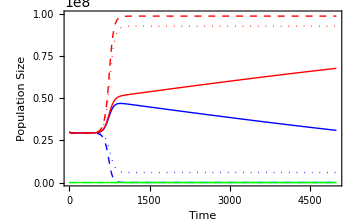
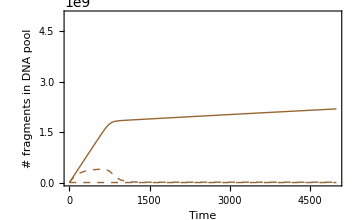

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion-> 1},ffunction,{t,0,100000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0.1,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion->1},ffunction,{t,0,100000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->10,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion -> 1},ffunction,{t,0,100000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

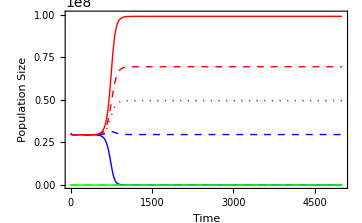
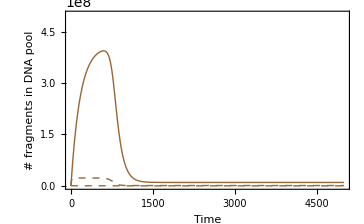

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion-> 1},ffunction,{t,0,100000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0.1,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion->1},ffunction,{t,0,100000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->10,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion -> 1},ffunction,{t,0,100000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

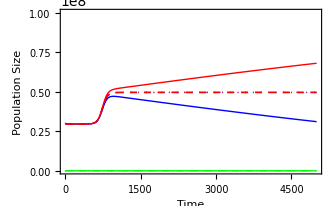
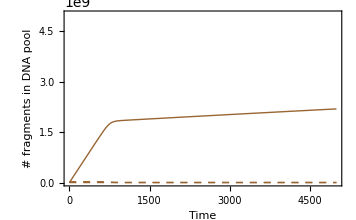

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

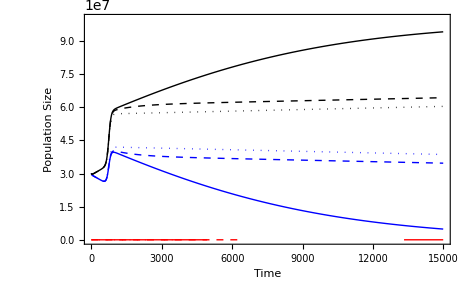
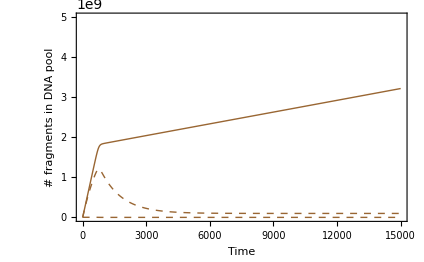

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

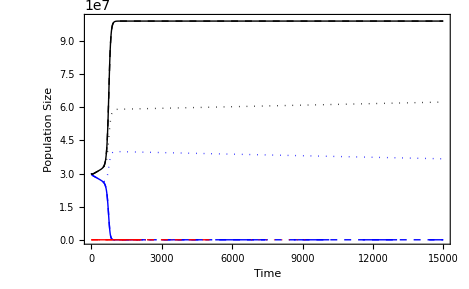
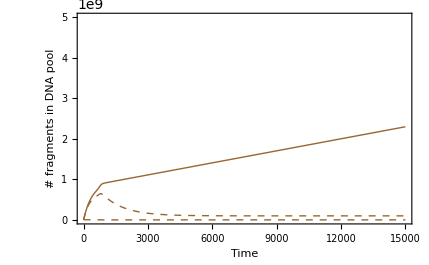

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];
```

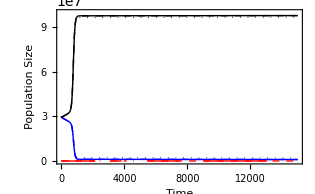
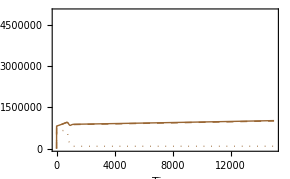

```mathematica
sol2=NDSolve[sys1/. {selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

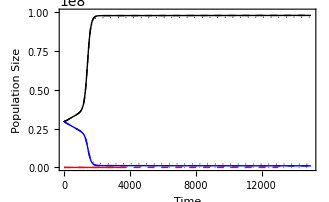
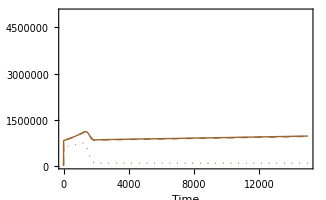

```mathematica
sol2=NDSolve[sys1/. {selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

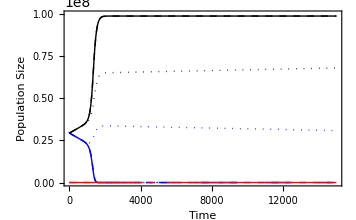
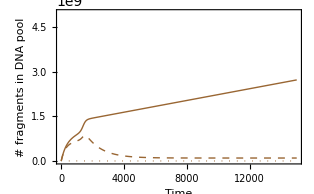

```mathematica
sol2=NDSolve[sys1/. {selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000000000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];(*Green,Method->"StiffnessSwitching"*dotted*)
```

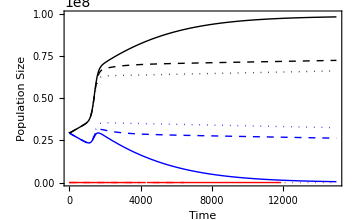
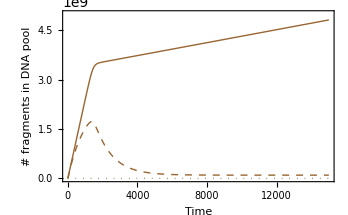

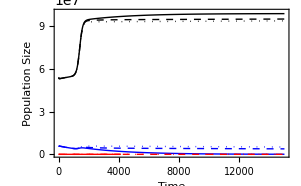
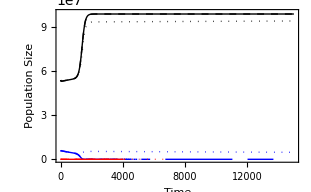
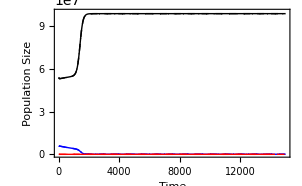

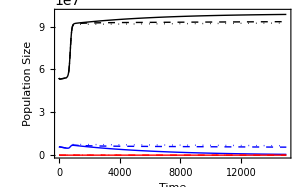
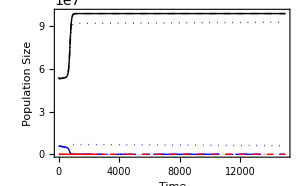
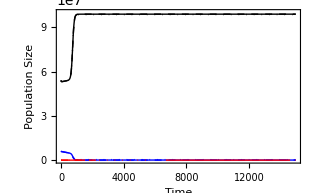

5000

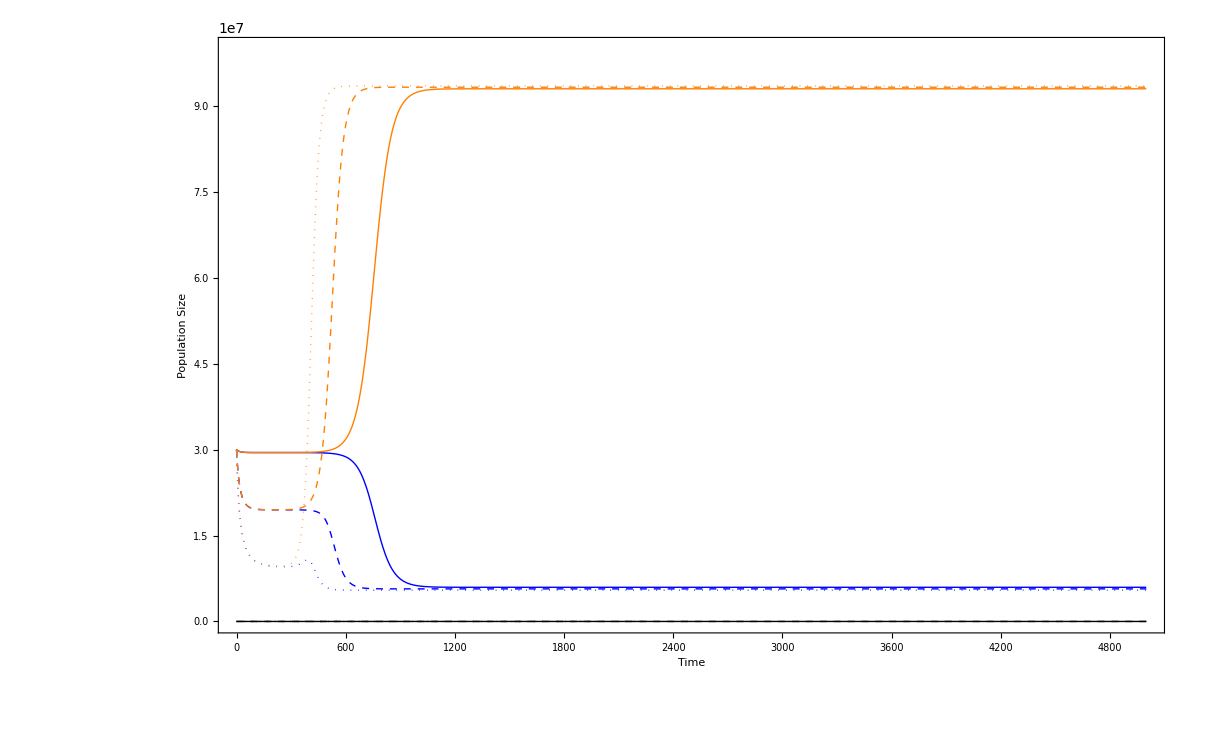

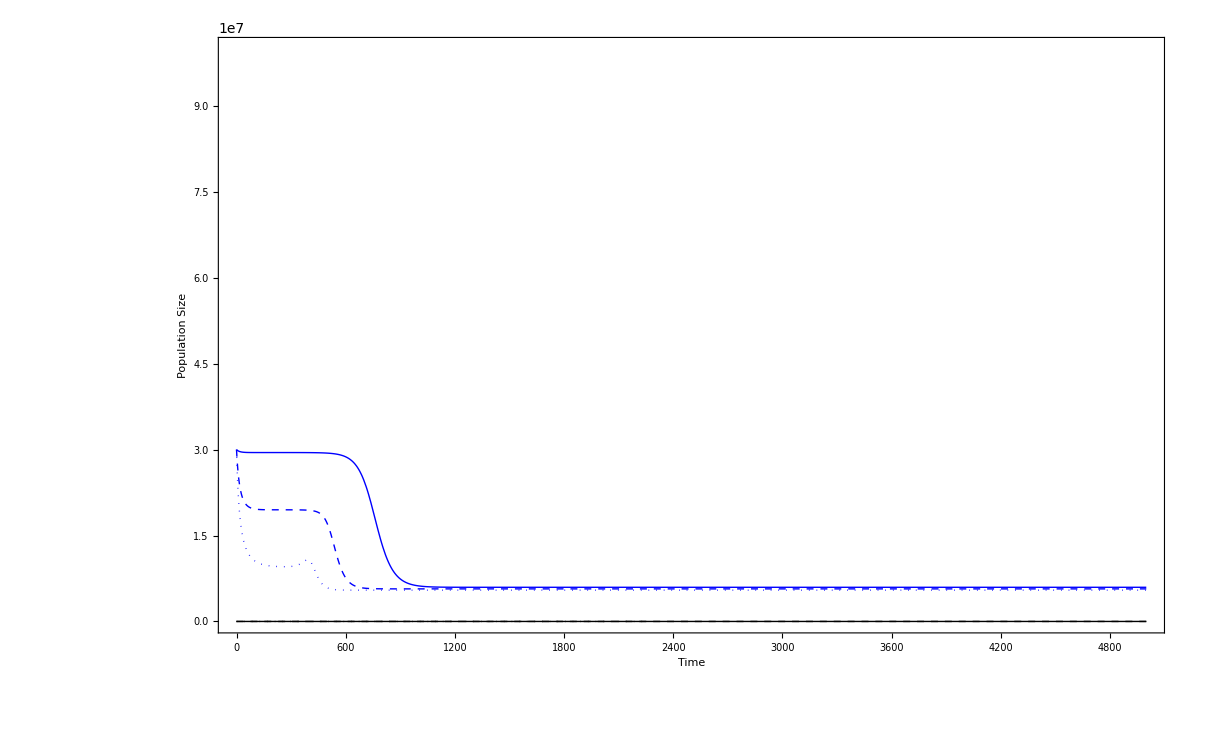

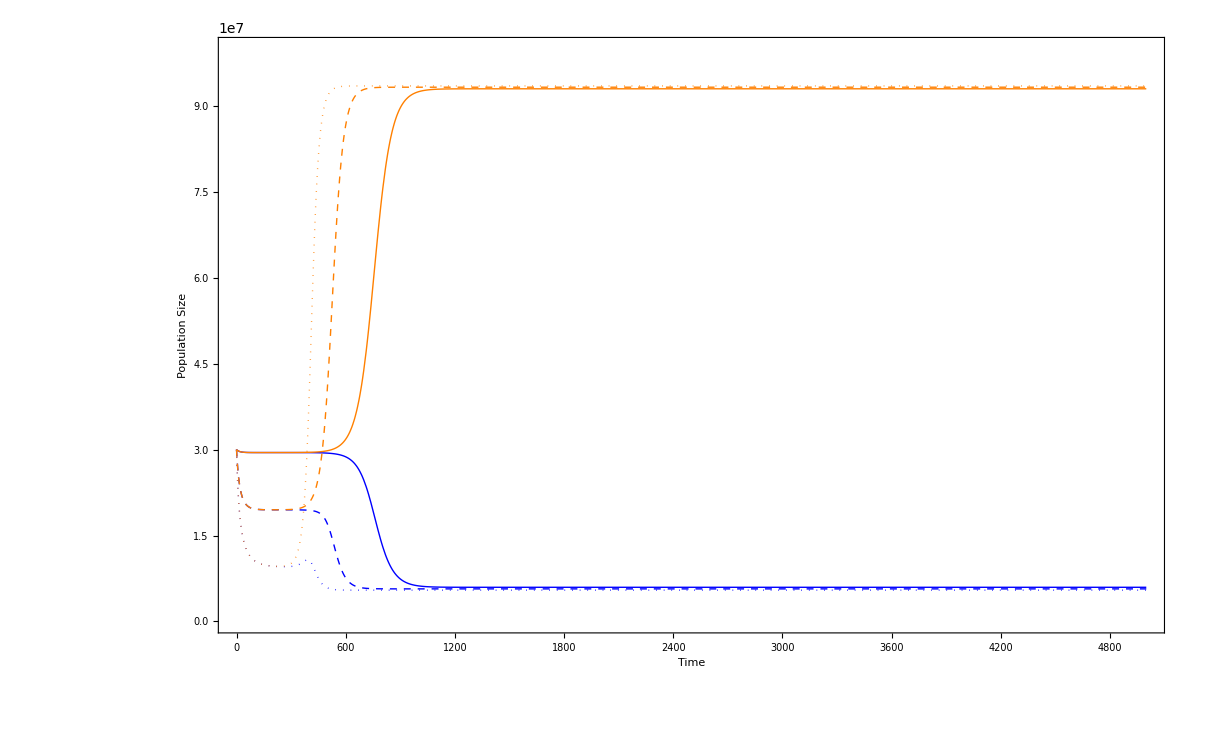

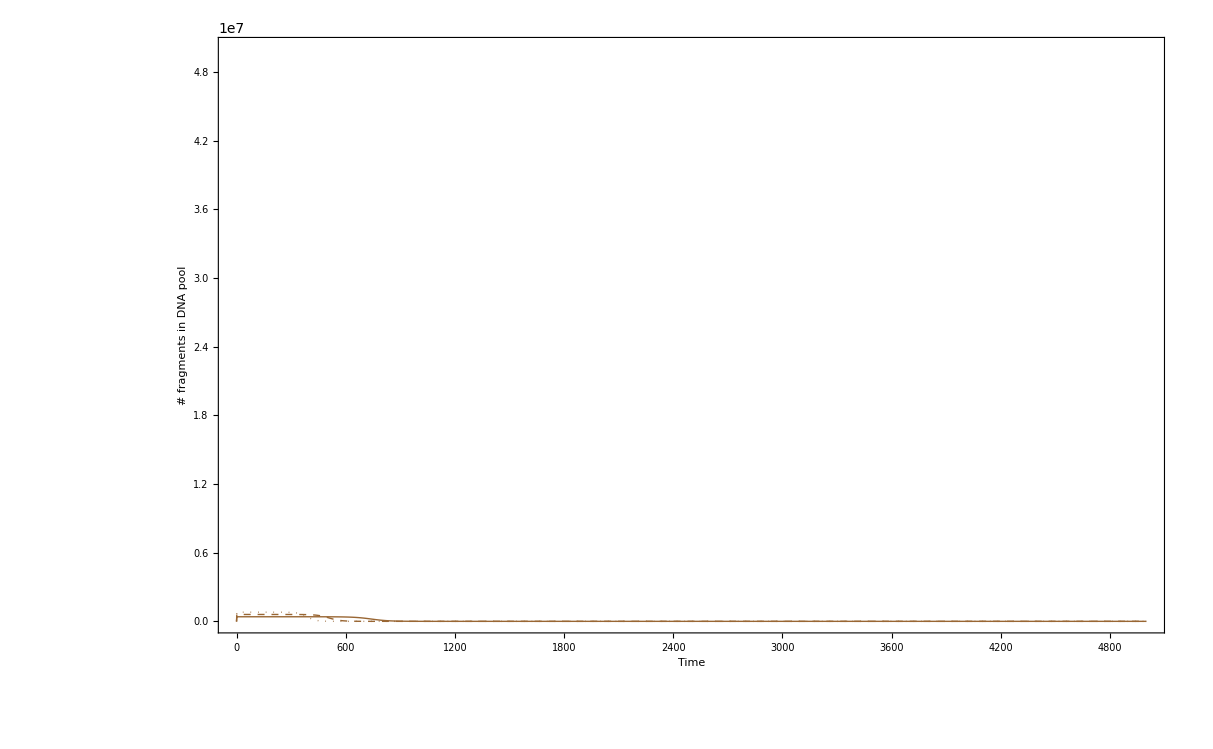

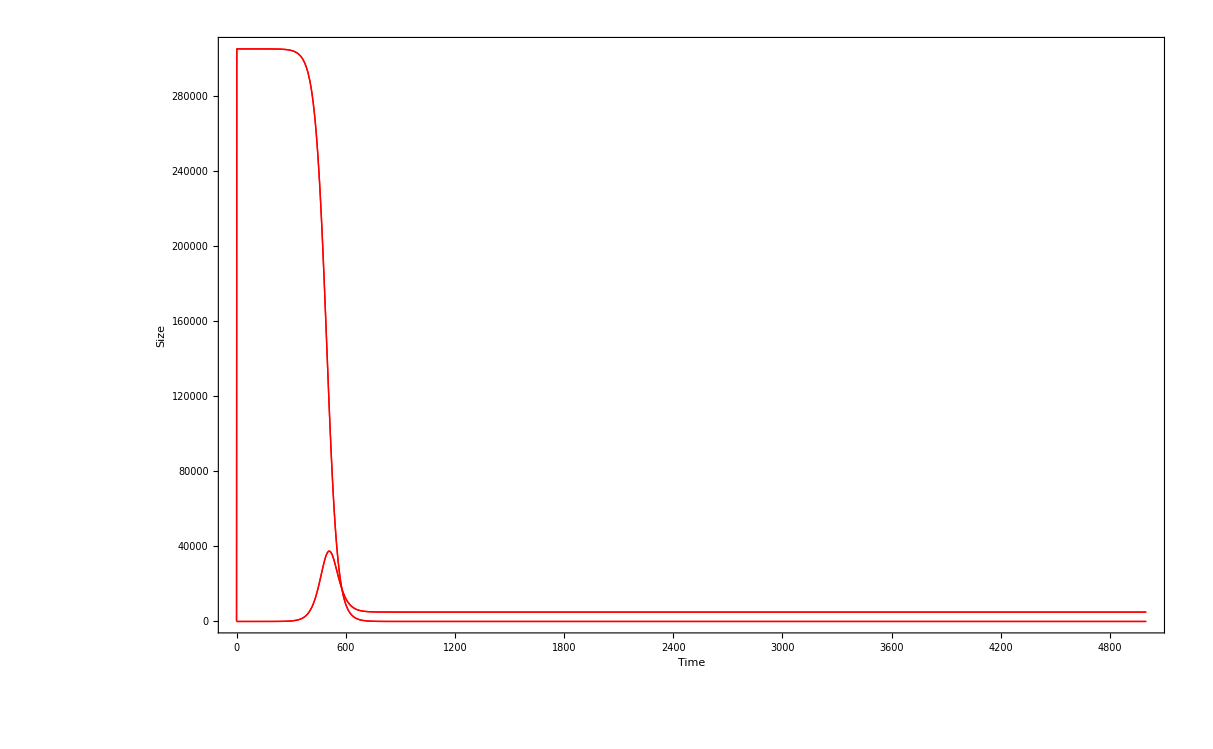

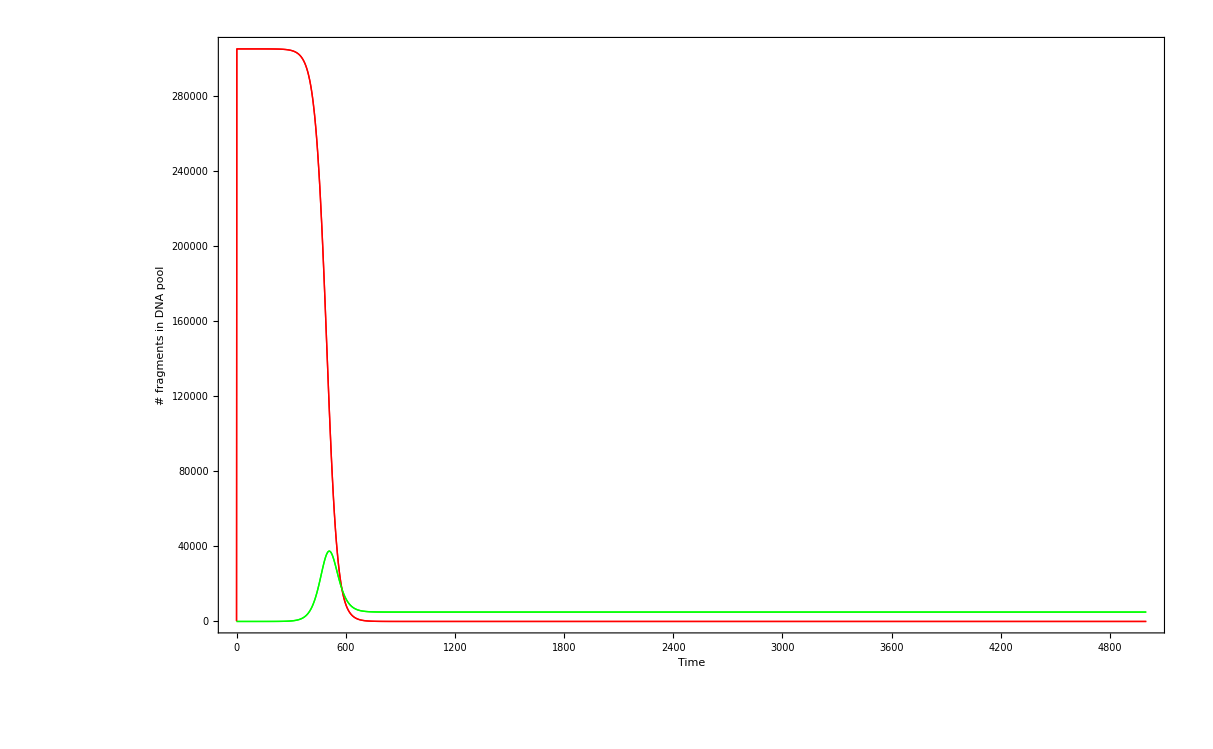

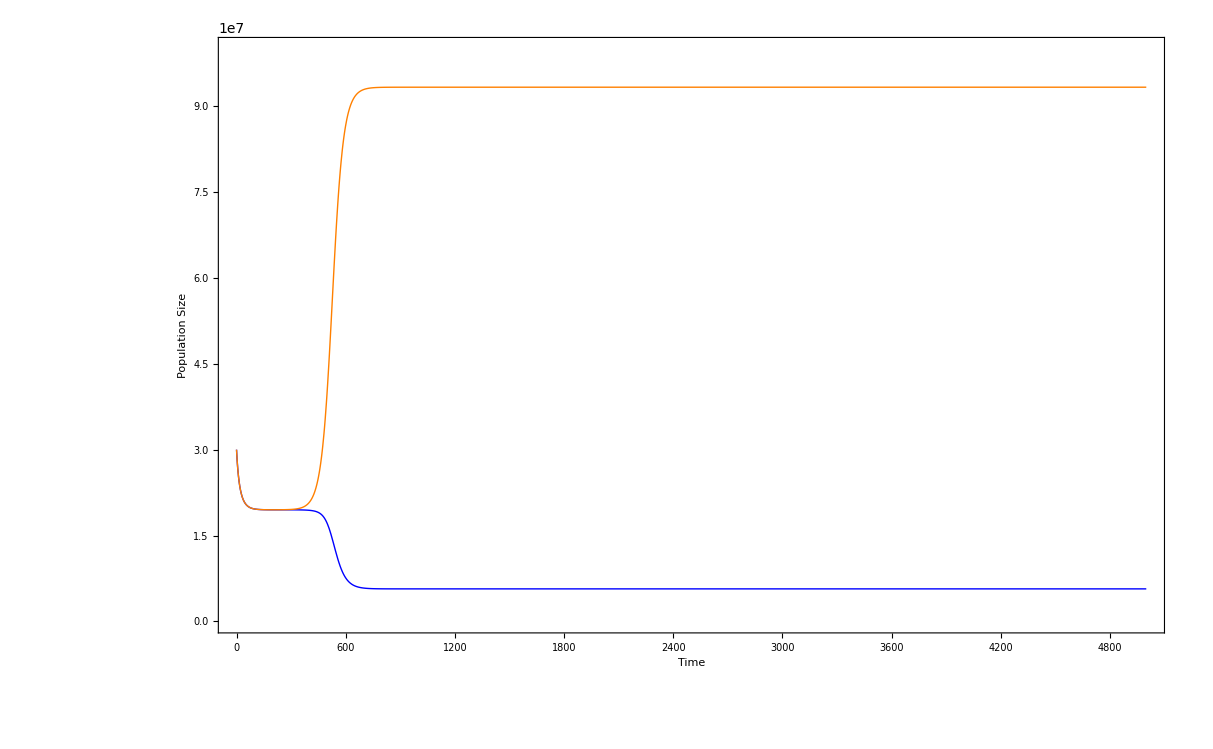

```mathematica
g=5000
Show[
Plot[Evaluate[rec  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{ Blue,Thick}]
,
Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle ->{ Blue,Dashed,Thick}]
,
Plot[Evaluate[rec/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle -> {Blue,Dotted,Thick}]
,
Plot[Evaluate[nut  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{ Orange,Thick}]
,
Plot[Evaluate[nut  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Orange,Dashed,Thick}]
,
Plot[Evaluate[nut/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Orange,Dotted,Thick}]
,
Plot[Evaluate[non /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{Black,Thick}]
,
Plot[Evaluate[non  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Black,Dashed,Thick}]
,
Plot[Evaluate[non/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Black,Dotted,Thick}]
,


 Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]


Show[
Plot[Evaluate[rec  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{ Blue,Thick}]
,
Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle ->{ Blue,Dashed,Thick}]
,
Plot[Evaluate[rec/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle -> {Blue,Dotted,Thick}]
,
Plot[Evaluate[non /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{Black,Thick}]
,
Plot[Evaluate[non  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Black,Dashed,Thick}]
,
Plot[Evaluate[non/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Black,Dotted,Thick}]
,


 Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]

Show[
Plot[Evaluate[rec  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{ Blue,Thick}]
,
Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle ->{ Blue,Dashed,Thick}]
,
Plot[Evaluate[rec/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle -> {Blue,Dotted,Thick}]
,
Plot[Evaluate[nut  /.sol2],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity}, LabelStyle->16 ,PlotStyle ->{ Orange,Thick}]
,
Plot[Evaluate[nut  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Orange,Dashed,Thick}]
,
Plot[Evaluate[nut/.sol4],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16,PlotStyle ->{Orange,Dotted,Thick}]
,
 Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]


RangeFragments=50000000;
Show[
Plot[Evaluate[sumf  /.sol2],{t,0,g},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,RangeFragments}, LabelStyle->16 ,PlotStyle -> {Brown,Thick}]
,
Plot[Evaluate[sumf /.sol3],{t,0,g},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,RangeFragments},LabelStyle->16 ,PlotStyle ->{Brown,Dashed,Thick}]
,
Plot[Evaluate[sumf/.sol4],{t,0,g},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,RangeFragments},LabelStyle->16,PlotStyle -> {Brown,Dotted,Thick}]
, Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]

Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle ->{ Red,Hue[StringCount[Convert[(m-3*2^locus+1)/2,locus-1],"1"]/(2^(locus-2))]}],{m,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]],
Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16},FrameLabel->{"Time","Size"}
]

Show[
Plot[Evaluate[ffunction[[3*2^locus+1]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle ->{ Red,Thick},
Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16},FrameLabel->{"Time","# fragments in DNA pool"}],

Plot[Evaluate[ffunction[[3*2^locus+2]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle ->{ Green,Thick},
Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16},FrameLabel->{"Time","# fragments in DNA pool"}],

Plot[Evaluate[ffunction[[3*2^locus+3]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle ->{ Red,Thick},
Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16},FrameLabel->{"Time","# fragments in DNA pool"}],

Plot[Evaluate[ffunction[[3*2^locus+4]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle ->{Green,Thick},
Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16},FrameLabel->{"Time","# fragments in DNA pool"}]]


Show[
Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle ->{ Blue,Thick}]
,
Plot[Evaluate[nut  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Orange,Thick}]
,
 Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]
```

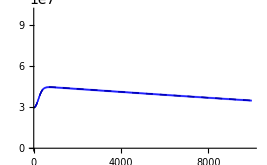

```mathematica
Show[
Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle ->{ Black,Thick,Dashed}],
Show[
Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.04],Blue},PlotRange -> {0,capacity}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}] ,BaseStyle->{FontFamily->"Arial",FontSize->16}]]
```

```mathematica
meanj=0;
Mean[sumf /.sol2]
time=10000;
up=0;
While[up<time,
holder=Evaluate[sumf /.sol4]  /.{t-> time};
meanj=meanj+holder;
up=up+1;
]

Print[meanj/up]
```

InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]+InterpolatingFunction[{{0.,1.5×10^7}},<>][t]

{2.57435×10^9}

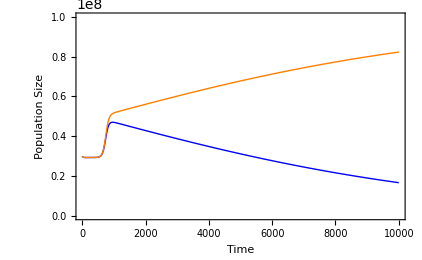
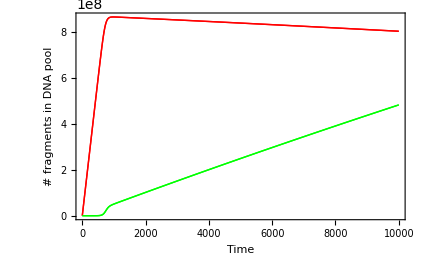

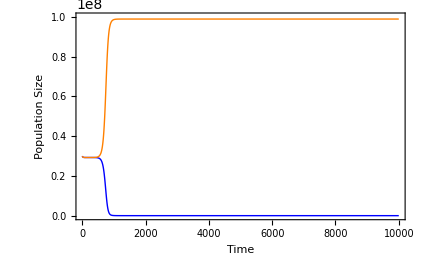
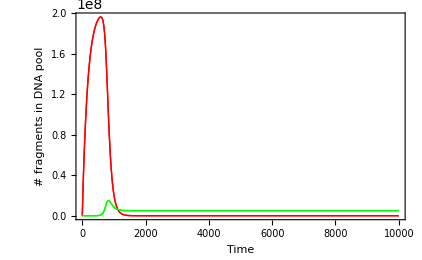

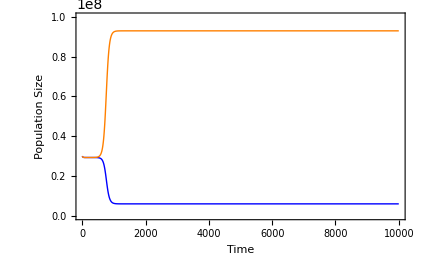
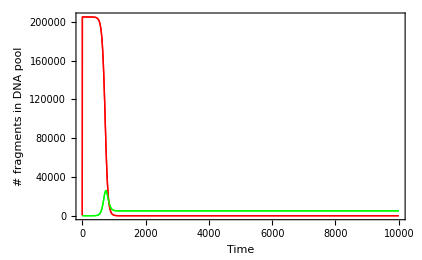

# Plots

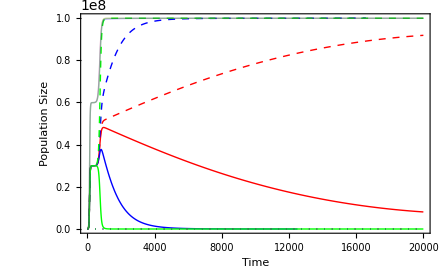

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion-> 1},ffunction,{t,0,10000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.000000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion-> 1},ffunction,{t,0,10000}];(*Blue*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.00000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion -> 1},ffunction,{t,0,10000}];(*Green,Method->"StiffnessSwitching"*)
```

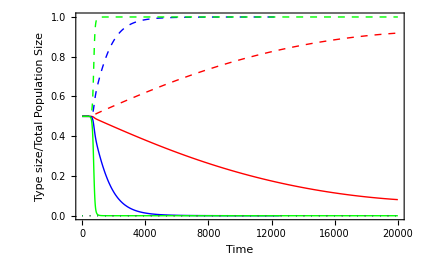
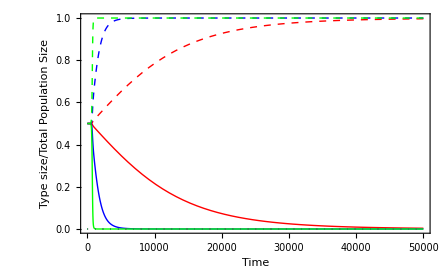

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion-> 1},ffunction,{t,0,100000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion->0.75},ffunction,{t,0,100000}];(*Blue*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion -> 0.5},ffunction,{t,0,100000}];(*Green,Method->"StiffnessSwitching"*)
```

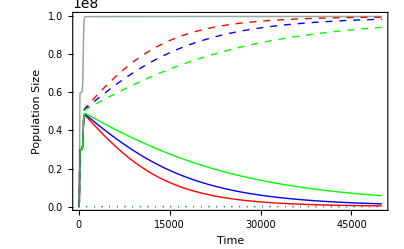
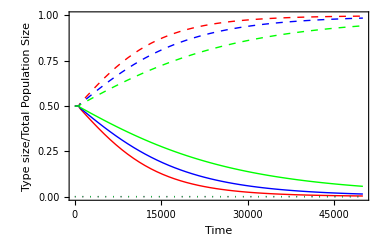

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion-> 1},ffunction,{t,0,100000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0.001,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion->1},ffunction,{t,0,100000}];(*Blue*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0.01,mutation->0.00000001, death->0.0001,cost ->0.00001,fratricide ->0,portion -> 1},ffunction,{t,0,100000}];(*Green,Method->"StiffnessSwitching"*)
```

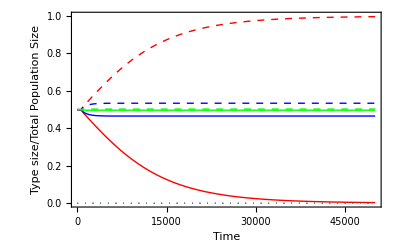
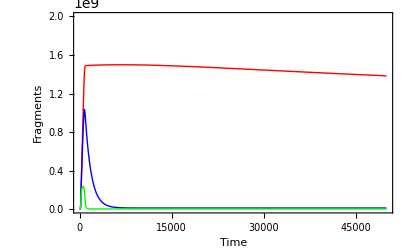

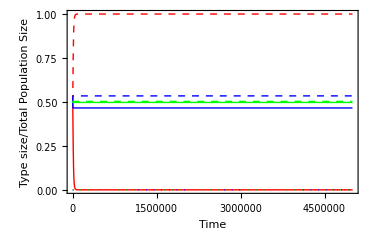
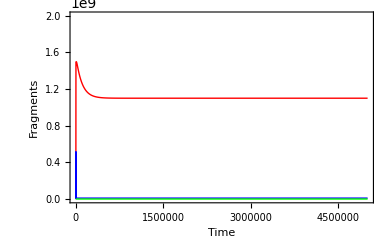

```mathematica
sol2=NDSolve[sys1/. {selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.00001,fratricide ->0,portion-> 1},ffunction,{t,0,100000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.00001,fratricide ->0,portion->1},ffunction,{t,0,100000}];(*Blue*)
sol4=NDSolve[sys1/.{selection->0.02,foodvalue->0.00001,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.00001,fratricide ->0,portion -> 1},ffunction,{t,0,100000}];(*Green,Method->"StiffnessSwitching"*)
```

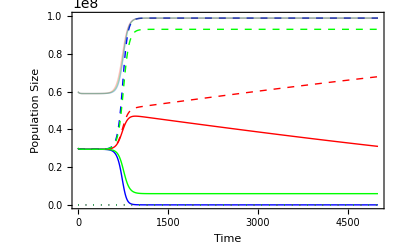
```mathematica
a1=-Graphics-
```

-Graphics-

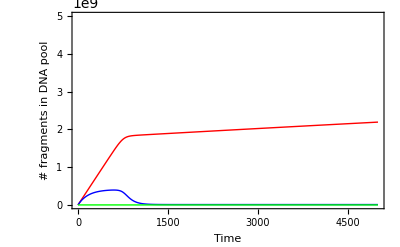
```mathematica
a2=-Graphics-
```

-Graphics-

```mathematica
a=GraphicsRow[{a1,a2},AspectRatio->0.6]
```

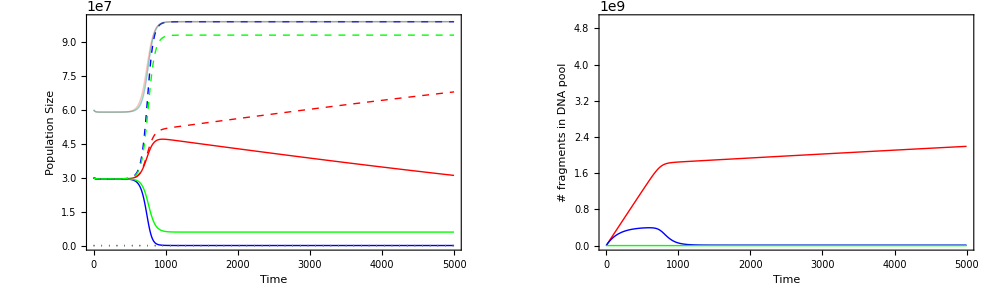

```mathematica
A
```

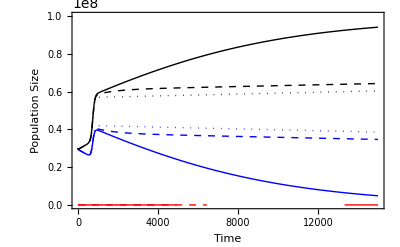
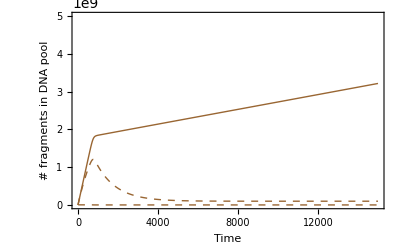
```mathematica
a1=-Graphics-;a2=-Graphics-;
a=GraphicsRow[{a1,a2},AspectRatio->0.6]
```

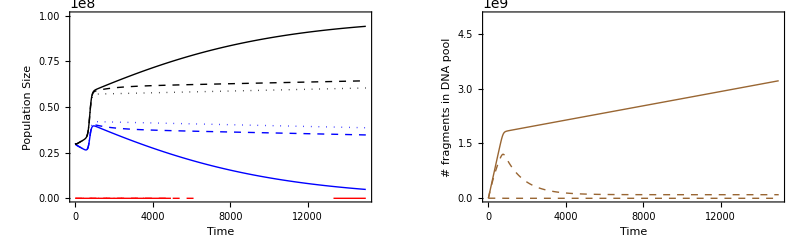

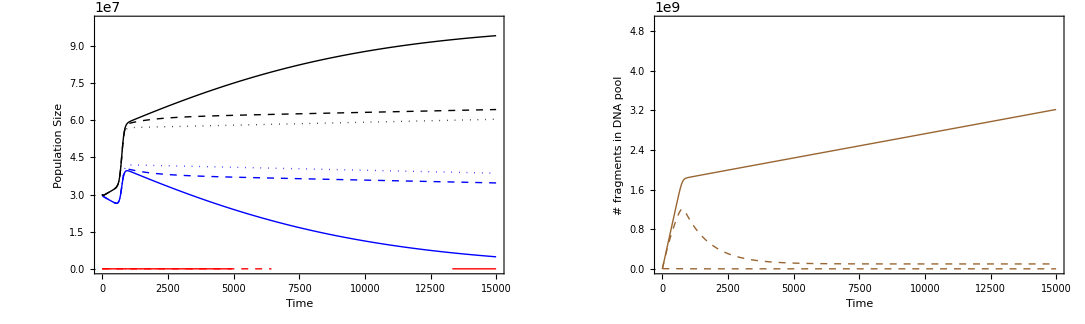

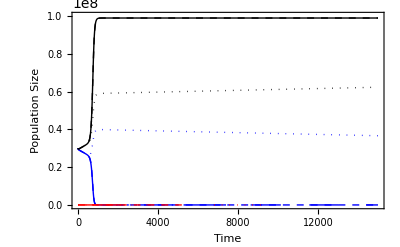
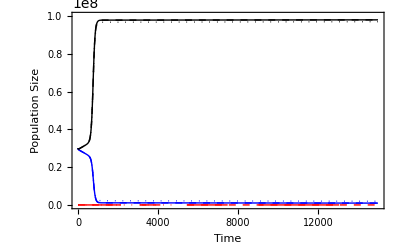
```mathematica
b1=-Graphics-;
b2=-Graphics-;
b=GraphicsRow[{b1,b2},AspectRatio->0.6]
```

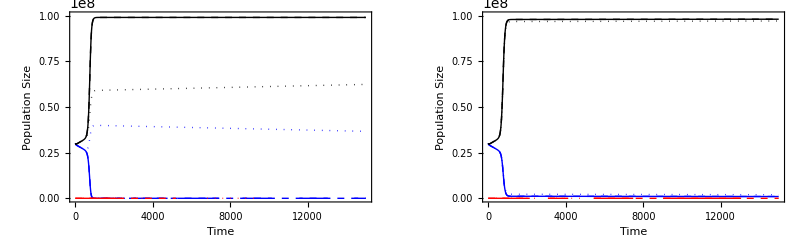

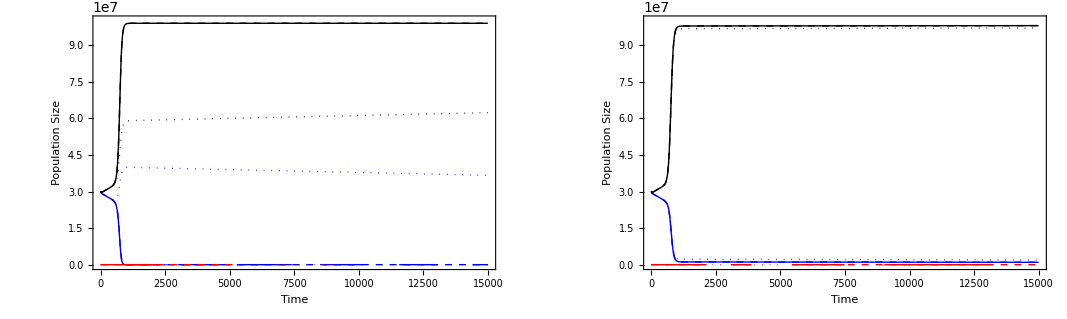

```mathematica
b=GraphicsGrid[{{a1,a2},{b1,b2}},AspectRatio->0.6]
```

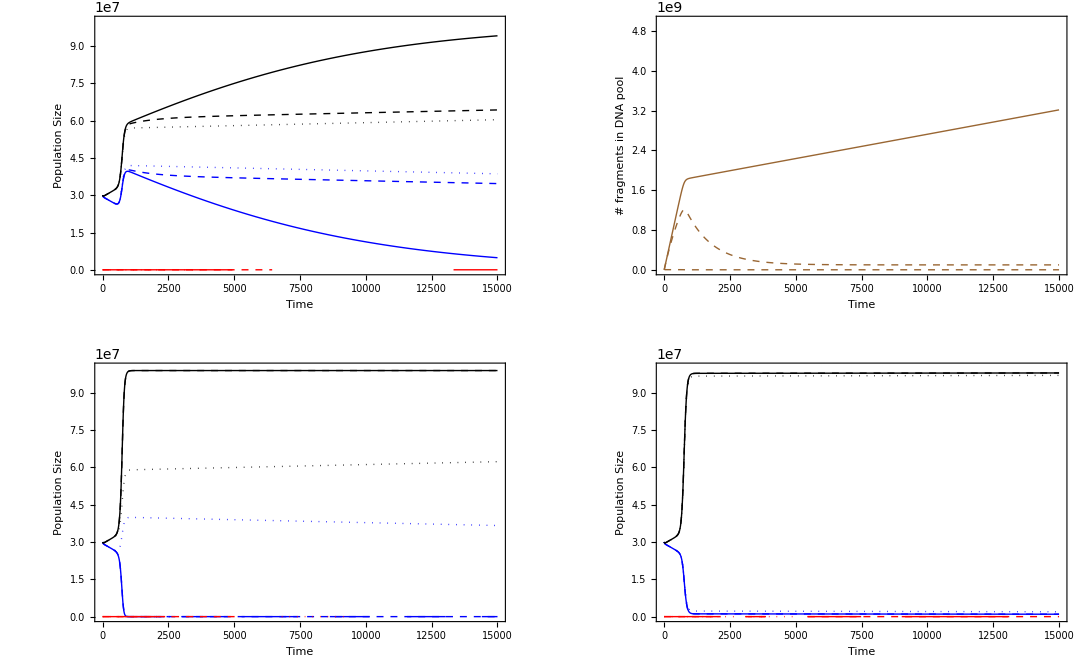

## two loci -13 -10 -7

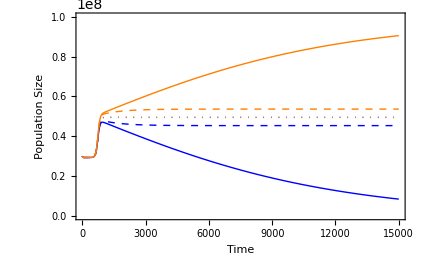
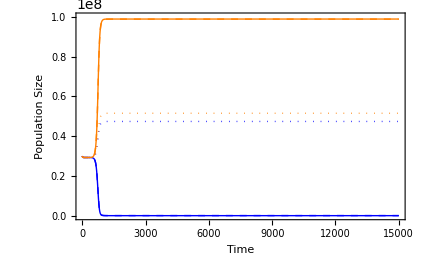
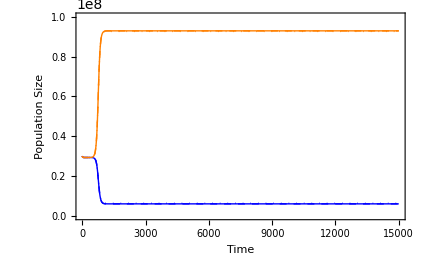

## four loci -13 -10 -7

```mathematica
sol2=NDSolve[sys1/. {selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion-> 1},ffunction,{t,0,15000}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->0.001,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion->1},ffunction,{t,0,15000}];(*Blue*dashed*)
sol4=NDSolve[sys1/.{selection->0.01,foodvalue->0,basegrowth->0.1, uptake->0.0000001,degredation->1,mutation->0.00000001, death->0.001,cost ->0.001,fratricide ->0,portion -> 1},ffunction,{t,0,15000}];
```

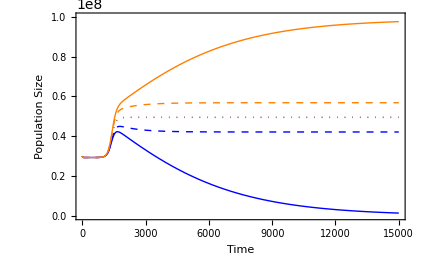
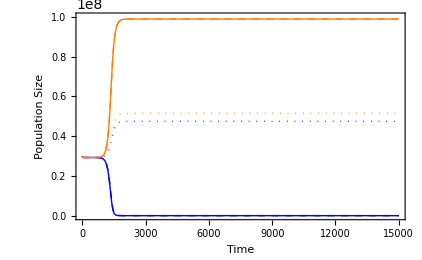
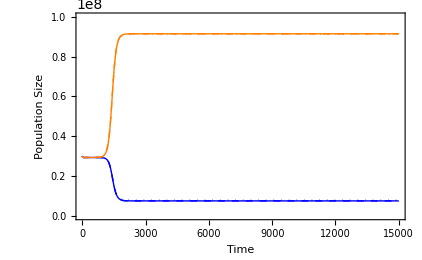

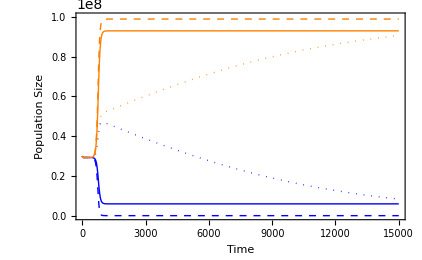
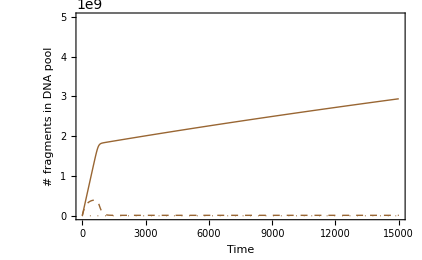

## two locus

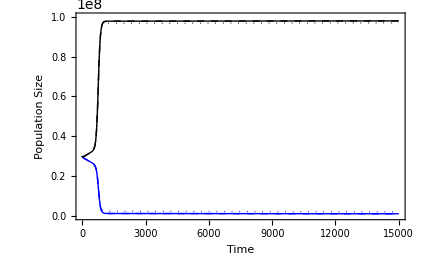
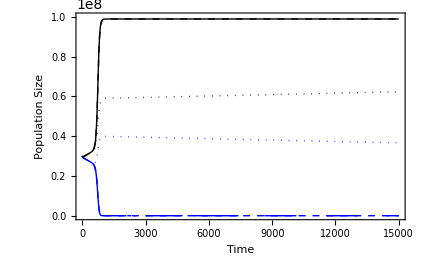
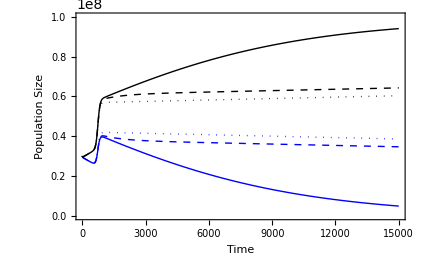

## Demostration

```mathematica
Show[Table[
Show[Table[ListPlot[Frag[[n]][[m]], Joined -> True,PlotStyle ->{Opacity[0.08],Hue[StringCount[Convert[n/2,locus-1],"1"]/(4*2^(locus))]},PlotRange ->All],{m,1,replicate}]]
,{n,1,2^(dnasize)*(locus-dnasize+1)}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","# fragments in DNA pool"} ,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
```

IntegerDigits::int: Integer expected at position 1 in IntegerDigits[3/2].

General::stop: Further output of IntegerDigits :: int will be suppressed during this calculation.

-Graphics-

IntegerDigits::int: Integer expected at position 1 in IntegerDigits[3/2].

General::stop: Further output of IntegerDigits :: int will be suppressed during this calculation.

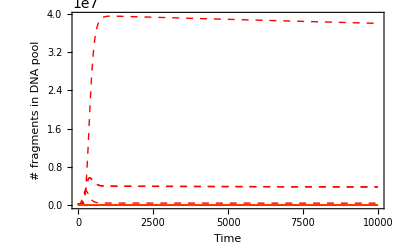

```mathematica
Show[
Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,10000}, PlotRange->All, PlotStyle -> {Hue[StringCount[Convert[n/2,locus-1],"1"]/(4*2^(locus))],Dashed,Thick}],{m,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]],FrameLabel -> {"Time","# fragments in DNA pool"} ,
Frame -> True,FrameStyle -> 16
]
,
Show[Table[
Show[Table[ListPlot[Frag[[n]][[m]], Joined -> True,PlotStyle ->{Opacity[0.035],Hue[StringCount[Convert[n/2,locus-1],"1"]/(4*2^(locus))]},PlotRange ->All],{m,1,replicate}]]
,{n,1,2^(dnasize)*(locus-dnasize+1)}],Frame -> True,LabelStyle -> 18,BaseStyle->{FontFamily->"Arial",FontSize->16}
]

,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
```

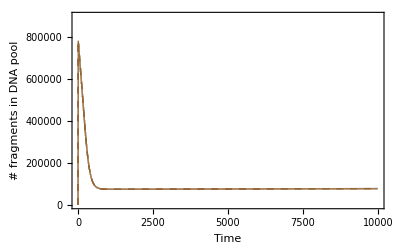
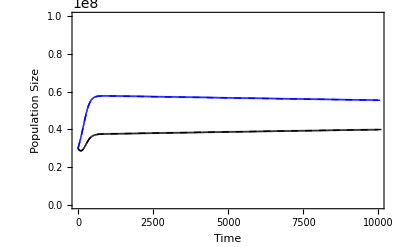
```mathematica
a2=-Graphics-;a1=-Graphics-;
```

```mathematica
GraphicsRow[{a1,a2},AspectRatio-> 0.64]
```

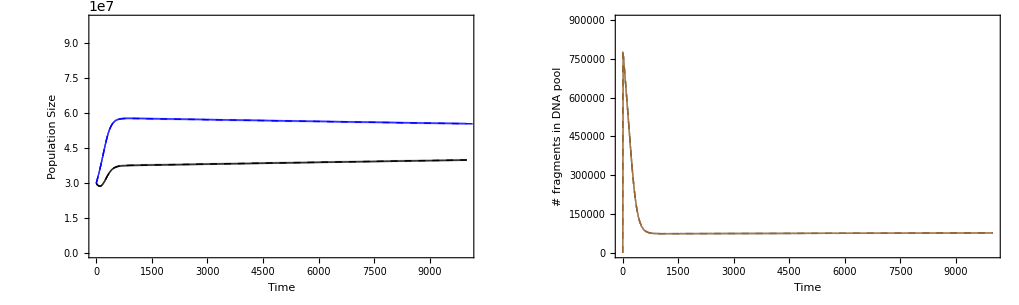

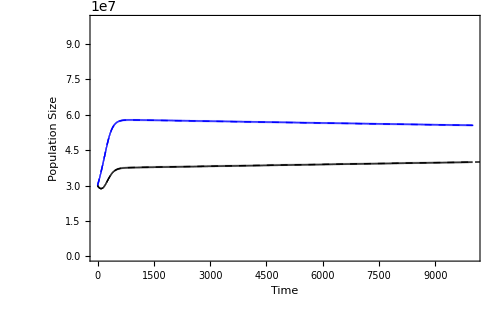

```mathematica
Show[
Show[
Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.03],Black},PlotRange -> {0,capacity}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.03],Blue},PlotRange -> {0,capacity}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}] ,BaseStyle->{FontFamily->"Arial",FontSize->16}]
,

Show[

Plot[Evaluate[rec  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle ->{ Blue,Dashed,Thick}]
,
Plot[Evaluate[non  /.sol3],{t,0,g},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> {Black,Dashed,Thick}]
,
 Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]]
```

```mathematica
Show[
Show[
Plot[Evaluate[sumf /.sol3],{t,0,10000},FrameLabel->{"Time","# fragments in DNA pool"},PlotRange ->{0,900000},LabelStyle->16 ,PlotStyle ->{Brown,Dashed,Thick}]
,
Frame -> True,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->16}
]
,
Show[Table[ListPlot[Fragsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.03],Brown},PlotRange ->All],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","# fragments in DNA pool"} ,BaseStyle->{FontFamily->"Arial",FontSize->16}]]
```

-Graphics-

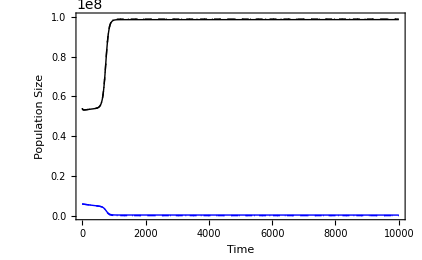
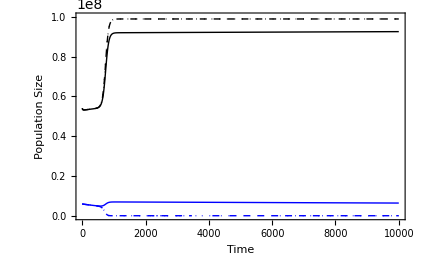
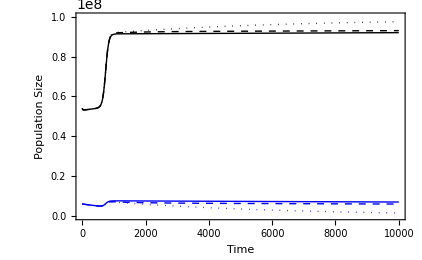

## Deterministic Model Fragments and population

```mathematica
a3=-Graphics-;a6=-Graphics-;
```

```mathematica
a2=-Graphics-;a5=-Graphics-;
```

```mathematica
a1=-Graphics-;a4=-Graphics-;
```

```mathematica
GraphicsGrid[{{a3,a2,a1},{a6,a5,a4}},AspectRatio-> 0.30]
```

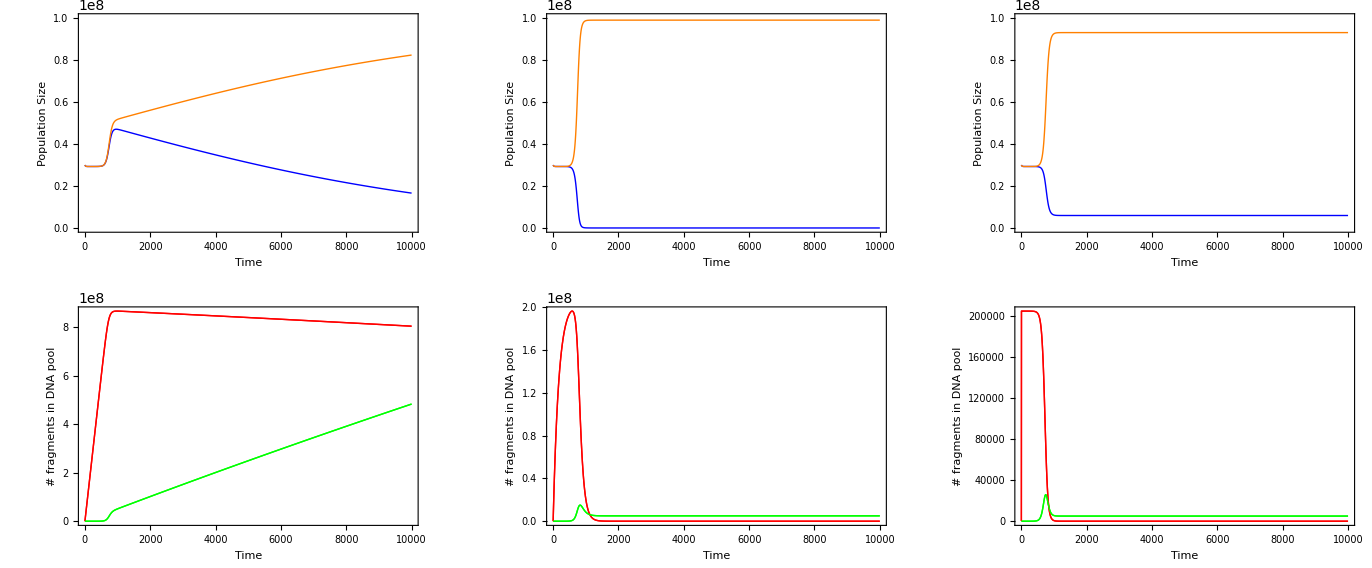

```mathematica
Print[∨]
```

```mathematica
∧
```

```mathematica
TextCell["∨",20,FontFamily->"Arial"]
```

∨

```mathematica
TextCell["∧",20,FontFamily->"Arial"]
```

∧

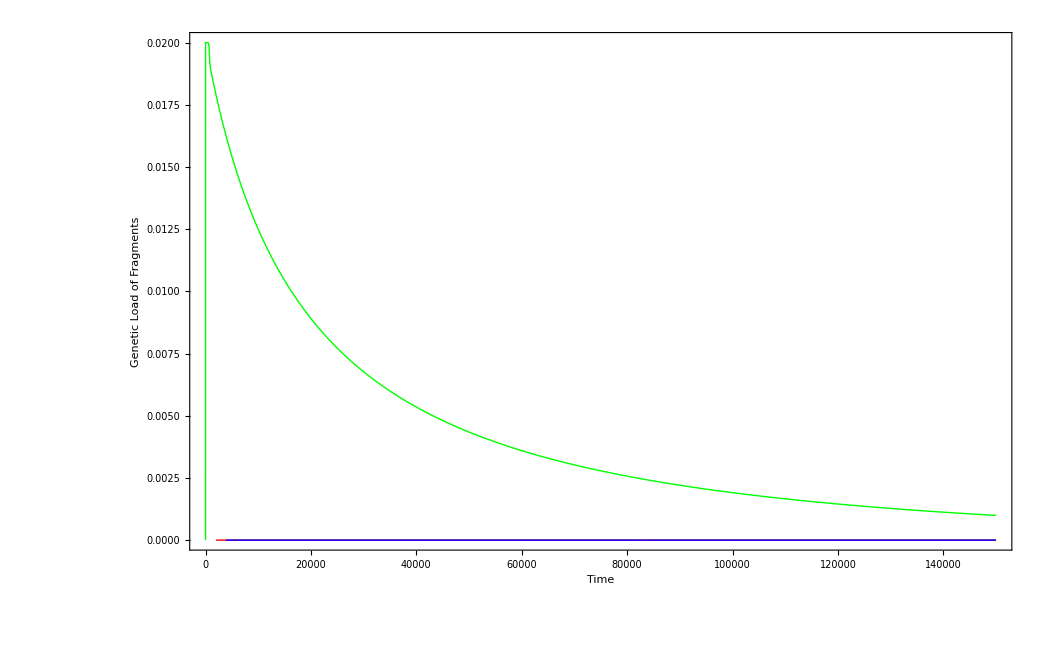

```mathematica
Print[Show[
ListPlot[mutloadf1,Joined -> True,PlotStyle ->Red],
ListPlot[mutloadf2,Joined -> True,PlotStyle ->Blue],
ListPlot[mutloadf3,Joined -> True,PlotStyle ->Green],Frame -> True,FrameStyle -> 15,PlotRange -> {0,0.02},AxesOrigin-> {0.01,0.02},FrameLabel->{"Time","Genetic Load of Fragments"}
]]
```

```mathematica
locus=1;
dnasize=1;
Clear[selection,foodvalue,basegrowth,uptake,degredation,mutation,death,cost,fratricide];
selection=selection;
foodvalue=foodvalue;
capacity= 100000000;
basegrowth=basegrowth;
uptake=uptake;
degradation=degredation;
mut=mutation;
death=death;
cost=cost;
fratricide=fratricide;
portion=portion;
Fitness=Table[0,{i,1,2^locus}];
Checkf[x0_, y0_,m0_]:=Module[{s1=x0,s2=y0,n=m0},s1=StringTake[s1,{n,n+StringLength[s2]-1}];StringMatchQ[s1,s2]]



Do[Fitness[[2^locus-i+1]]=((StringCount[Convert[i-1,locus],"1"]*selection))+death;,{i,1,(2^locus)}]

intitialff=Array[Subscript[ff,#][0]&,3*2^locus+2^dnasize*(locus-dnasize+1)];
initialf=Table[0,{i,3*2^locus+2^dnasize*(locus-dnasize+1)}];
initialf[[1]]=30000000;
initialf[[1+2^locus]]=0;
initialf[[1+2*2^locus]]=0;
ffunction=Array[Subscript[ff,#][t]&,{3*2^locus+2^dnasize*(locus-dnasize+1)}];
recombinationm=Table["",{2^locus},{2^dnasize*(locus-dnasize+1)}];
sizefrag=2^dnasize*(locus-dnasize+1);
derivationl=Array[Subscript[ff',#][t]&,{3*2^locus+2^dnasize*(locus-dnasize+1)}];
Do[derivationl[[i]]=0,{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}]
derivationr=D[ffunction,t];


sum=0;Do[sum=sum+ffunction[[i]];,{i,1,3*2^locus}];sum;
sumc=0;Do[sumc=sumc+ffunction[[i]];,{i,1,2*2^locus}];sumc;
sumf=0;Do[sumf=sumf+ffunction[[i]];,{i,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}];sumf;



Do[
s1=Convert[m-1,locus];
holder=StringTake[s1,{Quotient[(n-1),(2^dnasize)]+1,Quotient[(n-1),(2^dnasize)]+dnasize}];
s2=Convert[Mod[(n-1),(2^dnasize)],dnasize];
p=StringReplacePart[s1,s2,{Quotient[(n-1),(2^dnasize)]+1,Quotient[(n-1),(2^dnasize)]+dnasize}];
recombinationm[[m,n]]=p;
,{m,1,2^locus},{n,1,sizefrag}]
MatrixForm[recombinationm]


Do[derivationl[[n]]=derivationl[[n]]+ffunction[[n]]*(basegrowth+foodvalue*uptake*(sumf)-cost)*(1-(sum)/capacity)-ffunction[[n]]*Fitness[[n]];,{n,1,2^locus}]
Do[derivationl[[m]]=derivationl[[m]]-uptake*portion*ffunction[[m]]/sumf*ffunction[[3*2^locus+n]]; ,{m,1,2^locus},{n,1,sizefrag}]
Do[derivationl[[Binary[ToExpression[recombinationm[[m,n]]]]+1]]=derivationl[[Binary[ToExpression[recombinationm[[m,n]]]]+1]]+uptake*portion*ffunction[[m]]/sumf*ffunction[[3*2^locus+n]]; ,{m,1,2^locus},{n,1,sizefrag}]




Do[
Do[If[HammingDistance[Convert[n-1,locus],Convert[m-1,locus]]==1,
derivationl[[n]]=derivationl[[n]]+mut*ffunction[[m]]
]
,{m,1,2^locus}];
derivationl[[n]]=derivationl[[n]]- mut*locus*ffunction[[n]];
,{n,1,2^locus}]




Do[derivationl[[n]]=derivationl[[n]]+ffunction[[n]]*(basegrowth+foodvalue*uptake*(sumf)-cost)*(1-(sum)/capacity)-ffunction[[n]]*Fitness[[n-2^locus]];,{n,2^locus+1,2*2^locus}]
Do[
Do[If[HammingDistance[Convert[n-1,locus],Convert[m-1,locus]]==1,
derivationl[[n]]=derivationl[[n]]+mut*ffunction[[m]]
]
,{m,2^locus+1,2*2^locus}];
derivationl[[n]]=derivationl[[n]]- mut*locus*ffunction[[n]];
,{n,2^locus+1,2*2^locus}]
derivationl;


Do[derivationl[[n]]=derivationl[[n]]+ffunction[[n]]*(basegrowth)*(1-(sum)/capacity)-ffunction[[n]]*Fitness[[n-2*2^locus]]-sumc*fratricide*ffunction[[n]];,{n,2*2^locus+1,3*2^locus}]

Do[
Do[If[HammingDistance[Convert[n-1,locus],Convert[m-1,locus]]==1,
derivationl[[n]]=derivationl[[n]]+mut*ffunction[[m]];
]
,{m,2*2^locus+1,3*2^locus}];
derivationl[[n]]=derivationl[[n]]- mut*locus*ffunction[[n]];
,{n,2*2^locus+1,3*2^locus}]

Do[
derivationl[[n]]=derivationl[[n]]-degradation*ffunction[[n]];
,{n,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]

Checkf[x0_, y0_,m0_]:=Module[{s1=x0,s2=y0,n=m0},s1=StringTake[s1,{n,n+StringLength[s2]-1}];StringMatchQ[s1,s2]]
Do[
s2=Convert[Mod[(n-1),(2^dnasize)],dnasize];
If[Checkf[Convert[m-1,locus],s2,Quotient[n-1,(2^dnasize)]+1],
derivationl[[n+3*2^locus]]=derivationl[[n+3*2^locus]]+(ffunction[[m]]*Fitness[[m]])/(locus-dnasize+1);
derivationl[[n+3*2^locus]]=derivationl[[n+3*2^locus]]+(ffunction[[m+2^locus]]*Fitness[[m]])/(locus-dnasize+1);
derivationl[[n+3*2^locus]]=derivationl[[n+3*2^locus]]+(ffunction[[m+2*2^locus]]*Fitness[[m]]+sumc*fratricide*ffunction[[m+2*2^locus]])/(locus-dnasize+1);
];
,{m,1,2^locus},{n,1,2^dnasize*(locus-dnasize+1)}]

sys11=Join[  Table[ 0==derivationl[[i]],{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}]];


sys1=Join[  Table[ derivationr[[i]]==derivationl[[i]],{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}],Table[ intitialff[[i]]== initialf[[i]],{i,1,3*2^locus+2^dnasize*(locus-dnasize+1)}]];
sys1;

5000000
500000
50000
po=10000;
sol2=NDSolve[sys1/. {selection->0.0025,foodvalue->0,basegrowth->0.03, uptake->0,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion-> 1},ffunction,{t,0,po}];(*Red*)
sol3=NDSolve[sys1/.{selection->0.0025,foodvalue->0,basegrowth->0.03, uptake->10, degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion->1},ffunction,{t,0,po}];(*browne*dashed*)
sol4=NDSolve[sys1/.{selection->0.0025,foodvalue->0,basegrowth->0.03, uptake->0,degredation->0,mutation->0.00000001, death->0.001,cost ->0,fratricide ->0,portion -> 1},ffunction,{t,0,po}];(*blue,Method->"StiffnessSwitching"*dotted*)

rec=0;Do[rec=rec+ffunction[[m]],{m,1,2^locus}] ;
nut=0;Do[nut=nut+ffunction[[m]],{m,2^locus+1,2*2^locus}] ;
non=0;Do[non=non+ffunction[[m]],{m,2*2^locus+1,3*2^locus}] ;
```

(0 | 1
0 | 1)

5000000

500000

50000

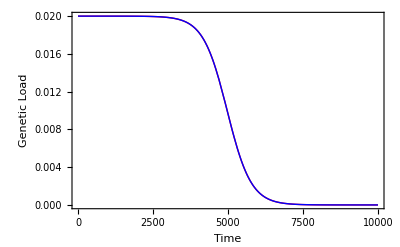

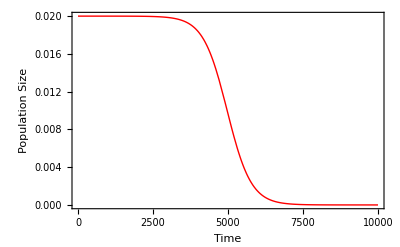

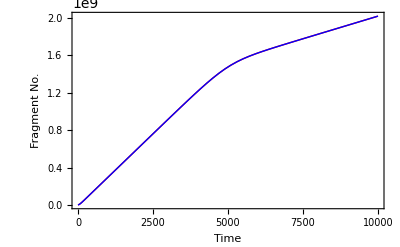

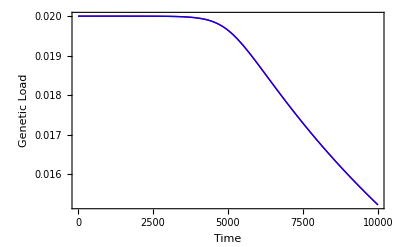

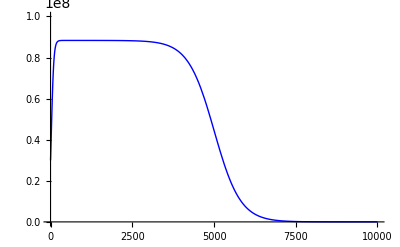

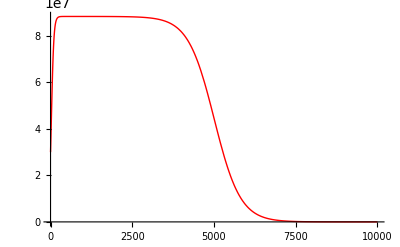

-Graphics-

```mathematica
Show[
Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Red,Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol3],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Brown,Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol4],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Blue,Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]



Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Population Size"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> Red,Frame -> True]

Show[
Plot[Evaluate[sumf  /.sol2],{t,0,10000},FrameLabel->{"Time","Fragment No."},PlotRange ->All,LabelStyle->16 ,PlotStyle ->Red],
Plot[Evaluate[sumf  /.sol3],{t,0,10000},FrameLabel->{"Time","Fragment No."},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Brown],
Plot[Evaluate[sumf  /.sol4],{t,0,10000},FrameLabel->{"Time","Fragment No."},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Blue]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]

Show[
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle ->Red],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])   /.sol3],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Brown],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol4],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> Blue]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]

Plot[Evaluate[ffunction[[1]]  /.sol4],{t,0,10000},FrameLabel->{"Time","Population Size"},PlotRange ->{0,capacity},LabelStyle->16 ,PlotStyle -> Blue]
Plot[Evaluate[ffunction[[1]]  /.sol2],{t,0,10000},FrameLabel->{"Time","Population Size"},PlotRange ->All, LabelStyle->16 ,PlotStyle -> Red]

g=po;
Show[
Show[
Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Red,Thick},Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol3],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Brown,Thick},Frame -> True],

Plot[Evaluate[ffunction[[1]]*0.02/(ffunction[[1]]+ffunction[[2]])  /.sol4],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Blue,Thick},Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
,
Show[
Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol2],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Red,Dotted},Frame -> True],

Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol3],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle -> {Brown,Dotted},Frame -> True],

Plot[Evaluate[ffunction[[3]]*0.02/(ffunction[[3]]+ffunction[[4]])  /.sol4],{t,0,10000},FrameLabel->{"Time","Genetic Load"},PlotRange ->{0,0.02}, LabelStyle->16 ,PlotStyle ->{Blue,Dotted},Frame -> True]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
,
Show[
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol2],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle ->{Red,Thick,Dashed}],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])   /.sol3],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> {Brown,Thick,Dashed}],
Plot[Evaluate[ffunction[[7]]*0.02/(ffunction[[7]]+ffunction[[8]])    /.sol4],{t,0,g},FrameLabel->{"Time","Genetic Load"},PlotRange ->All,LabelStyle->16 ,PlotStyle -> { Blue,Thick,Dashed}]
,Frame -> True,BaseStyle->{FontFamily->"Arial",FontSize->16}
]
]
```